## 1. Обучающий набор.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Studies\2 kurs\Neutral Networks\NG4P08 GolubovichRoman

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Partition[BinaryReadList[F,"Byte",ByteOrdering->+1],Rows Cols];
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Images, Digits}]
```

```mathematica
Map[Dimensions,Train=LoadMNIST["train"]];
```

```mathematica
Map[Dimensions,Test=LoadMNIST["t10k"]];
```

```mathematica
Xtest = Test[[1]]/255;
Ytest = Test[[2]];
Xtrain = Train[[1]]/255;
Ytrain = Train[[2]];
```

## 2. Трёхслойная нейронная сеть прямого распространения.

```mathematica
kmLayer[1]:=kmWeight.#&
kmLayer[2]:=SoftMax[#]&
```

```mathematica
kmLayer[2]
```

SoftMax[#1]&

### 2.1. Слой нейронов.

```mathematica
kmWeight = RandomReal[0.001*{-1,1},{10,784}];
```

### 2.2 . Функция активации.

```mathematica
SoftMax[X_]:=Quiet@Chop@(#/(Plus@@Exp[X]))&/@Exp[X]
```

### 2.3. Сеть прямого распространения.

```mathematica
ClearAll[kmANN];
kmANN=RightComposition@@Array[kmLayer,2]
```

kmWeight.#1&/*(SoftMax[#1]&)

```mathematica
kmANN[Xtest[[1]]];
```

## 3. Потери : перекрёстная энтропия, дельта правило.

```mathematica
curX = 6
```

6

```mathematica
PadRight[PadLeft[{6},curX],10]
```

{0,0,0,0,0,6,0,0,0,0}

```mathematica
ClearAll[kmLoss];
kmLoss[Y_List,Digit_Integer]:=-PadRight[PadLeft[{1},Digit+1],10].RealExponent[Y,ⅇ]
```

```mathematica
kmLoss[kmANN[Xtest[[1]]],Ytest[[1]]]
```

## 4. Дельта правило обучения.

```mathematica
ClearAll[kmTrain];
(**{Растр,Цифра}↦Градиент функции потерь**)
kmTrain[{X_,Digit_}]:=TensorProduct[PadRight[PadLeft[{1},Digit+1],10]-kmANN[X],X]
```

Потери тем меньше, чем меньше каждая координата вектора (YT-Y)

```mathematica
(*ΔW[{X_,Digit_},η_] := η*kmTrain[{X,Digit}]*)
```

```mathematica
kmTrain[miniBatch:{{_,_}..}]:=Total[Table[kmTrain[i],{i,miniBatch}]]
```

## 5. Подбор оптимальных параметров обучения.

```mathematica
kmTrain[miniBatch_Integer,η0_Real,Steps_Integer,W0_List]:=Block[{mytrain =Transpose[{Train[[1]]/255.,Train[[2]]}],Step=0, kmWeight = W0,η = η0,batches,number},
While[Step<=Steps,
batches =Partition[RandomSample[mytrain],miniBatch];
number=1;
While[Step<=Steps &&number<=Length[batches],
kmWeight += η*kmTrain[batches[[number]]];
number++;
Step++
];
η=0.66*η];Return[kmWeight]]
```

```mathematica
Dynamic@Step
```

```mathematica
kmWeight = RandomReal[0.001*{-1,1},{10,784}];
```

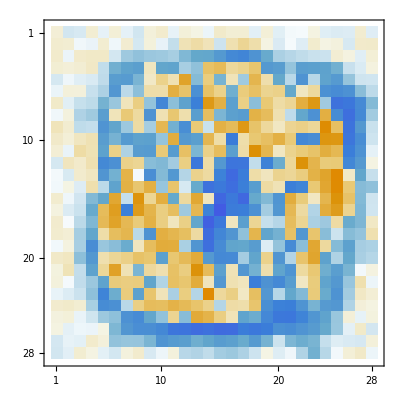
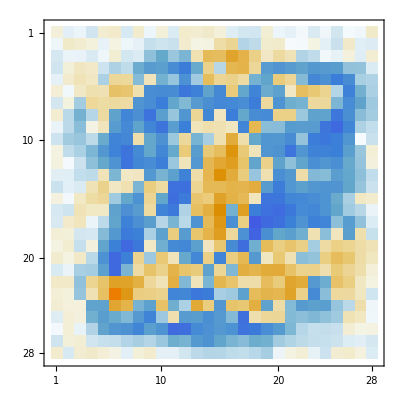
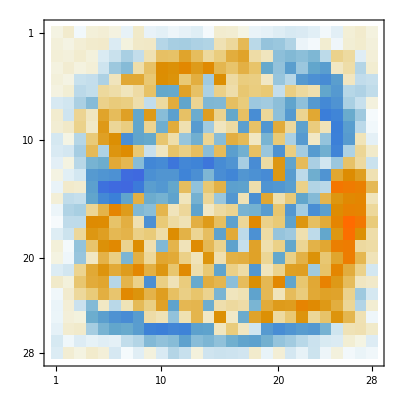
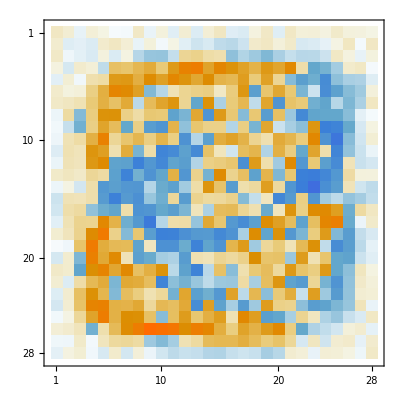
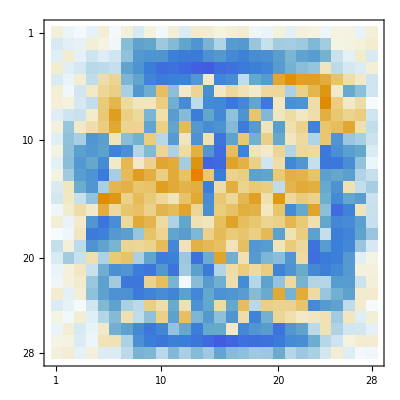
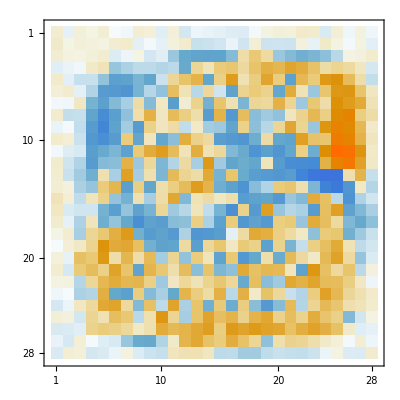
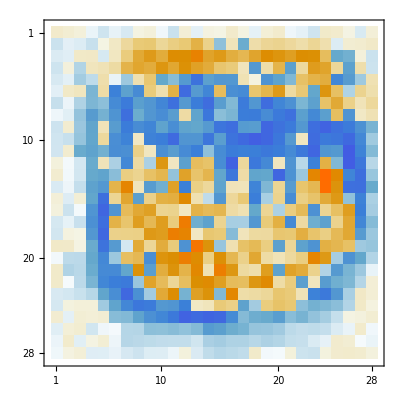
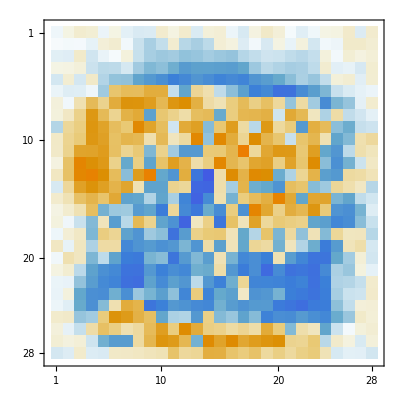

0.9164

```mathematica
kmWeight = kmTrain[10,0.1,30000, kmWeight];
Table[MatrixPlot[Partition[kmWeight⟦i⟧,28]], {i,10}]
res = ((First[TakeLargest[kmANN[Xtest[[#]]]->"Index",1]]-1)==Ytest[[#]])&/@Range[Length[Xtest]];Count[res,True]/Length[Xtest]//N
```

### Best Weights

```mathematica
kmWeight = {{0.00017619433861903837,0.00035151553913413463,1.5482024228984093*^-6,-0.000914188745241414,-0.00047973966912398134,0.00023993849801077398,-0.000037001484097807895,0.00044075235819583626,-0.00027052841892499313,0.0005165944068283549,0.0007194989550873372,-0.0001553405294955415,0.00024017680974247447,-0.00003980607014604542,-0.0005202530123747093,0.000620823197496825,0.0009008037998726424,-0.0008262897105743602,0.0009407351830573729,0.0005909691843744209,-0.0001336066677687939,-0.0007174221198868714,-0.0005721231444377243,0.0007118258908994754,0.0007629497490444807,0.0006184991356448766,0.0004131613806199687,0.0002631745090570319,-0.0006279946418111721,0.0009053253398908002,-0.0001124524953288711,-0.0003850002314312248,0.0008530189992131182,0.00035349842727336626,-0.0007449139958376773,0.000903547555317249,0.0006714213084681943,-0.004211842818582494,-0.06824391853941236,0.131370311790188,0.2874872490164862,0.11802683362011904,-0.003691821757825146,0.06443440995061364,0.2248458331914407,0.1236732175432764,-0.0005419495489794,-0.0003865632424920809,-0.0007937641590630006,-0.0009659274697492961,0.00030814865616641965,0.00022980635364864633,-0.00010423498450208698,-0.00039365934855845486,0.000056268157097006354,0.000225884257282454,0.00001766526436217629,-0.0007011028167431834,-0.000055988567531941886,0.015441792945801867,0.006061383915183696,-0.00194694099961216,-0.0084506892586353,-0.030052396278799,-0.07159983391546604,-0.16789958790612936,-0.18218878062903646,-0.11423196630147803,-0.1917942463960274,-0.36953210373245077,-0.5309481223448128,-0.6687051050814017,-0.6214907867835198,-0.5255213968761218,-0.3346835206226337,-0.35593904761077777,-0.35687248201914007,-0.10006835485406168,-0.0038342657451766065,-0.00004387819423495009,-0.00016092896007377538,0.00007800006530552547,0.0002568191401730673,0.0004891360558073629,0.0004318640388561966,-0.00012904009230574028,-0.0009329777368465219,0.04197522270771825,-0.04110940276867224,-0.24505910835309,-0.28912244914455065,-0.4652377252157321,-0.17135273864910258,-0.21840344777100448,-0.41904478297036785,-0.41906945393749157,-0.4312371175404752,0.32971885344059443,0.433072165126766,-0.031951487712087716,-0.15406341280079427,-0.19697651590401272,-0.43115149977314515,-0.6873241401835845,-0.3580521628027268,-0.5978150534314768,-0.4575587361855605,-0.11111480801461354,-0.012737336293313445,0.0022859489230896654,-0.0005128169776588464,0.0005630077667774088,-0.00019539084394199196,-0.0008537741859551309,0.0002735953786198073,0.0002802965841642891,-0.08880883529120136,-0.4783723233145369,-0.4500765122877475,-0.3441332601926082,-0.054580926706855194,0.41823411466834026,0.3776743722190331,0.9852386857533559,-0.3550920256343069,-0.2331659028458275,-0.4231489231786147,0.3043835725338413,0.064648991686947,0.5637418452382494,0.04448972168900478,-0.4756330057284157,-0.26799920756075296,-0.5359407167242631,-0.3423409543111505,-0.4847093699728478,-0.5810516239660275,-0.15270551780813468,-0.013618949555673348,-0.0006408500541685139,0.0008149529203791517,0.0007309355209004428,-0.0010583155637796217,-0.0061536506828704365,-0.23877970060152076,-0.7380097537175667,-0.4969327872497964,-0.221811431577666,0.1560211963222985,0.2194691029972744,1.2065133931422223,0.5968956228979526,-0.3256523770207125,0.5825471579381504,0.8310656845191752,0.28203316299197584,0.014313356254253574,0.4362868213999396,0.6618261580448811,0.12358749898940946,-0.745585988213298,0.0019631739703835104,0.4475654766838414,-0.3579334173101171,-1.0284308667770081,-0.5719737928640768,-0.13191067396255543,-0.038191488545415125,0.00032086764834651565,0.00026716822825851016,-0.0011117949291173323,-0.0002861422612273809,-0.33662420640251944,-0.3864184879155993,-0.09933960029336625,0.41374486127751875,-0.04180641201477919,-1.0454248550602252,0.1994804755544382,-0.0499860696783477,-0.6439963011489911,1.1492276360443794,0.5941554360281464,-0.42040814438186,-0.029001688443690863,0.007691501377273323,0.6957152845328269,0.6067245354592964,0.4567909664884651,0.9098325036425697,1.9525009216870777,0.34205876198455365,-1.618906559857561,-1.3515440870906867,-0.4643340456718032,-0.10092903714233101,-0.0007259179552342016,-0.0009461104225438677,0.00023097722180009773,-0.004672426694111157,-0.3615253905439902,-0.05703572544609038,0.3089588719741671,0.17820403290056774,-0.8949126678224265,-0.23282162042794505,0.23202889841500363,0.3668736467885558,0.15698044554061572,1.4282646011684668,0.42849591928904823,-0.095740315042347,-0.530572529263253,1.095073997032976,0.647654781488201,0.7191164065244772,0.3660466537714535,-0.2168218162881895,0.021100285053315564,0.8773809366988635,-0.29445474407905964,-1.4131646666246804,-0.6497442882409786,-0.0704194871859379,0.05385708163241387,0.0004549988688503539,0.005721227048824952,0.05442727679983887,-0.506540560863852,-0.34186250298939724,-0.12594550996881815,-0.21887998523206437,-0.2169044253560088,0.6060731711988887,0.14941165654313557,0.1546599115031417,0.7196482293549373,-0.2855682090307754,1.2172614648128177,1.033216065671888,1.6195679091864317,1.0909775027878355,0.7527404987449707,-0.5438115629104487,0.6709500424665797,0.4021855417257666,0.7046987727281967,1.5726305397790805,0.6432181974930158,-1.662452238472521,-0.6016704812128979,-0.06594718933412139,-0.00033186954873008377,-0.000183929854967805,0.03561536819325979,0.15668882961564862,-0.37944535653098627,-0.07784479869932386,-0.2958338321188186,-0.6995829729057083,-0.5672735925986518,-0.14059882796512035,0.817571276542114,-0.46951671975115716,0.18693062907793737,1.0964128176331214,0.2165559689412676,-1.3900777818739214,0.048533849013616466,0.2946634456223362,1.0900964628172634,0.7743854392039877,0.35378638825053105,-0.5237418630531884,-0.9800555204454099,1.4283909269784156,1.4576106720614623,-1.7586199932122941,-0.6199367726718021,-0.0016129095815157653,0.0007825101438424398,0.00011595370904826684,0.1741985529194649,0.13797641590912663,-0.27922875101820605,0.7997160670468246,-0.23494633223561195,-0.9022064030035799,-0.005888922357044419,0.5197111880503761,-0.5997280466752644,1.1256547009427749,-0.3165420608638702,0.9086003923876512,0.3566335618045921,-0.7644185733855077,-0.1898288494150276,1.2039460745556656,0.858247383171225,0.04599078646730051,0.2921918711686749,0.2875237208704291,0.4358613203833211,1.4285068289855811,1.3414874721401606,-1.623424634437518,-0.5984123496179501,-0.00016831049608223217,0.00023364305397672105,0.03275803528924216,-0.0005139892470073954,0.16322584442772517,-0.7178034844864274,-0.2025612964002383,-0.2967275049378925,-0.386480243177766,-0.24487852963844992,-0.6472053645041769,-0.3267626130226328,0.25886005938757156,-1.1335480109710687,0.14334153505815472,-1.0893209004282285,-1.7814278862978588,-1.342867057667465,0.3274212471391881,-0.6313230824846024,0.36558666322111893,0.48839215720753243,1.2654607042525408,0.873644693726772,0.826472523756747,1.006309596620847,-1.1136960742950663,-0.43659415464456647,-0.0005165785738331357,-0.0005380575531544478,0.00018449025652568098,-0.0002792689056065482,0.06398273498840547,-0.37043127738576437,0.1836059535069922,0.4304928311435546,-0.11726255283828985,-0.5011305088734742,-0.14771336851892533,-0.09634195398058149,-0.018630646489940547,0.6957215663008868,-0.059159998337960186,-1.705379924244779,-2.488476405201009,-1.4591154806007607,-0.3131962829359904,-0.1185298271571803,0.669469016264215,0.5384368109670477,0.7343220634461612,1.214354980819052,1.243457943286889,2.067328521212243,-0.011065519229866818,-0.26397840047305937,-0.0020226861702983545,-0.0008872172245859887,-0.00022331074874709197,-0.00007904633701185029,0.0586198269353539,0.5566047100256597,0.11446252139469885,0.9823092073112,0.5976084208283355,0.5426690998721684,0.02434946094312864,0.8740253131174166,0.15450677407927227,0.42172224140242315,-1.7604141515526304,-1.9174781128031677,-2.3452189194500677,-1.4221461629506247,-0.6688384416038572,0.008292241733952365,-0.2750064273880807,-1.0664446129531593,-0.3084159649314487,0.7147111574159406,1.2176177070086105,1.4799144268285171,0.31028936456142625,-0.05864308703585548,-0.02324008525903648,0.0003065974406493006,0.0006558165535228548,-0.0008955902639143632,-0.32082945827471704,0.11133072504385098,1.2155645847320395,0.2493980381610525,1.5344993795108919,0.6582990027638929,0.8206030056780632,0.03959856427310502,0.3670870612770373,0.8114595938533115,-0.5184079459823245,-2.369128927822852,-2.262327252460014,-2.364626876755227,-0.13582500288728871,-0.24624413944640886,-0.4457563532036447,0.12498764301868348,0.28672623272916314,0.2061791274123533,1.3954383631778975,1.587805293483174,0.3199127257370377,-0.03012623194846795,-0.000293553117188321,-0.0005075023670174933,-0.000921979360267948,-0.003776574388534604,-0.5002902035792095,0.3483194826135284,1.5268986737317305,-0.9873969374525654,0.976519830440842,0.6954001565745636,0.8848661381307734,0.3149232554296261,-0.21147679090979382,0.5592222406136971,-1.8000049002811083,-2.9658890390494226,-1.998967303621729,-1.3424314810747426,-0.9589638336017559,-0.3858477284000495,-0.3004580380567302,0.44923335182137203,-0.2266747073009903,0.521995341550888,1.201216433883906,1.269589221534425,0.20612199104050163,-0.0839682311722269,-0.01446601138398056,-0.0009414740802513883,0.00025579329048592674,-0.033422899889391705,-0.49859521157493314,0.4385196453425708,1.159332686367761,0.3288085255842963,0.17101789908079076,1.2409281716049056,0.363391464636426,0.31409365532464995,0.7092586452313256,-0.731630401064322,-2.9937023188314797,-1.976032751114422,-0.4610273140135343,-0.7418832897552758,-0.03388702852128615,0.1353845950297313,0.6941683609731322,0.6652143125734191,0.2376724386441462,-0.2433523230509099,0.48743312727207355,0.27865055614280265,-0.2714403676101274,-0.24672958375286919,-0.027788174703492548,-0.0004450256901031178,-0.0002057023774517018,-0.0781567990382167,-0.4082495220609867,0.5219350108909943,1.217232388560863,0.5253112982721259,0.25759463052160825,0.0076103047299929455,0.6648642223361861,1.3216238104614029,0.5072752586236603,-0.5261647610385897,-2.2994616321073464,-1.4227820331436039,-0.442523141461477,-0.14781297314617323,0.5197233664554837,-0.20334209689986496,0.078761540234426,0.6392420530326852,-0.38589705289860887,0.08275919023328589,0.0006300397648397027,0.368533639389209,-0.12383975822378655,-0.11142196946147757,0.08059323797163738,0.0006511730897766571,-0.0009385568394268385,-0.040914387294282185,-0.49319318859848116,-0.13975547308987937,0.2601627021705491,-0.34683486564341937,0.47946092009904107,0.7759702453548808,1.3107292967393174,1.1380292542032504,0.18352108237916281,-0.5195607148723317,-1.2722448359304916,-0.671871134645696,-0.11807287982213543,-0.3553438433336682,-0.5409419557468388,-0.2016599463253642,-0.34525460765787885,-0.8472092238833957,-0.1628293374420714,0.900725034620453,-0.06946439184947457,0.18043732418932296,-0.18461233413897885,-0.07796238909141331,-0.053076263587254764,-0.00024062941546366783,0.029995118622901072,0.017451123913577657,-0.29254608475620003,-0.44155765899983884,0.18711894566457885,0.3325107176102262,1.069667139773365,0.758008430486251,0.07186552841930949,0.8036691333171146,1.1016220146972693,1.10965834251063,-0.48409207908478763,-1.0497463881705127,-0.7454497993010227,-0.6842486970984382,0.00333884707809141,0.02294740034082251,-0.08532025383381228,0.3483856878886388,0.7136702287252534,0.9973089595062642,0.040660993046758395,0.21315076002181946,-0.2628075511836993,-0.1254418549919447,0.0005087268280595576,0.0005870045865841874,0.07450493061463895,0.001083306854295501,-0.27938458782958525,0.0031422405514089295,0.8977782404697954,0.6946254744738001,0.20655552732517737,0.7076745739028387,0.16376785832436447,0.7818291259754317,0.8229202494296516,1.8047912846589187,0.47749110300562747,-0.4721562602772264,-0.410282633084484,-0.53228261769304,-0.02908862943964194,-0.402759985594991,-0.019011542947963856,-0.3538055060202172,0.2501863496914994,0.6191608816703107,-0.30612811788995486,-0.19903516315005532,-0.1839626165123418,0.00030973374062719165,0.0006791150316012187,-0.00020413460800490805,-0.0009409357479143029,-0.09685380861921772,-0.11277703768528653,-0.45870927596969846,0.5264800838355652,0.5619462182297543,-0.09790933460031344,-0.23937636140235524,0.4069869511126637,0.711675617145381,1.3463116818436387,0.5465247912566704,-0.07534815752394403,-0.06823277329000314,0.19011263993452943,0.2139267283537868,-1.0558806024962453,-0.896132880167153,-1.1901499488708536,-0.530546567298171,0.07789245193312014,0.18182231258682796,-0.15622754181314377,-0.25775552247992345,-0.09192512867030334,0.09797343633498816,-0.0002461559369731409,0.00018091988874000984,-0.0003632963368393211,-0.012577845952217339,-0.38061420276751157,-1.3612980786839854,-0.13693504156770803,0.46770240665265794,0.08256793754871519,0.5858961032101634,0.33644300912740954,-0.01471341122256859,0.29422510642905403,0.15213043115335934,1.819584767627982,-0.06167202034184868,0.06729288782329836,-0.11791695999688505,0.0692518418263519,-0.7187070025361267,0.05623607459403189,-0.33745585458235744,-0.21223762458683704,0.15869649763270954,-0.15741472259362016,-0.26964796235766253,-0.1090901764230163,0.010719294355906848,-0.0006223133182783049,-0.0005599386448247807,-0.00048156281980786097,-6.0776177322939115*^-6,-0.22647507921357773,-1.2683896236080636,-0.9879152133394078,-0.4061588302639549,0.27198481197062074,0.5578204297145196,0.8197268528422842,0.9728029496279633,0.8695832174413751,0.23330047332287696,0.5647099192144552,0.4125990533191785,0.03599182875618093,-0.1738030134132697,0.5290542779543498,-0.6988995083650866,-1.0342534512062915,-1.139457743226873,-0.7386103021528508,-0.2792742676929488,-0.32745061902246453,-0.22926659667551977,-0.09062229030886515,0.0008060957786170158,0.0002810366645102161,-0.00018374437984779732,-0.0006093857806090089,0.00037826277698175365,-0.00027766155593509577,-0.2169155789306363,-0.3925900968423279,-0.5810922697388412,-0.6397169898134702,-0.6629848190972012,-0.18640435877914377,-0.17700264732897344,-0.17719156212018175,0.9296971026478223,0.6305811272953059,0.5068530696831594,-0.1793353755425116,-0.2788522588549519,-0.41956601207847166,-1.1192583807975791,-1.1329743694244703,-1.0960269646939762,-0.8645244912742446,-0.39940127561455735,-0.1978248534693304,-0.020175668916152315,-0.008621825268035517,0.0003702404277560853,0.0004650043424761544,0.00048235824821430155,0.0004757808058100826,0.00031313633321815304,0.0006862872812459931,0.0003530426930436482,-0.058972085670403074,-0.5557994906956436,-0.9271384256287032,-1.1238435375360558,-1.3792749457839164,-1.6413824541255164,-1.6379215065085302,-1.9847327302744218,-1.4784652566876595,-1.869956451807504,-2.0718670818782123,-1.430407096451571,-1.4751755875935264,-1.2740838621639905,-0.6835841647494023,-0.7297007447671938,-0.7696783631373321,-0.37502673157714395,-0.11394341892804623,-0.0005614338424930461,0.0002764120087502069,0.0008757176052928959,0.00011130348223673588,-0.000198777852318025,-0.00046509648797047297,-0.00021754227706747165,0.0005563655864543782,-0.0000901607824489384,0.0008095969502773882,-0.11169572463185751,-0.2455782687273348,-0.3246328172201595,-0.39208382472108877,-0.23666673307457847,-0.145578676053695,-0.0912406406986485,-0.4233138544417415,-0.5379806605461059,-0.42789947342420315,-0.228645328688763,-0.4278373382062576,-0.23200271893815103,-0.03725009233592619,-0.2370274125777279,-0.4228593436727009,-0.2882550049750351,-0.048910656513701724,-0.0007789702762715868,-0.0008936743530883269,-0.0007746360613977233,-0.00010592094343837974,-0.0006475670572237257,-0.0006403493802833323,0.0003871267897517165,0.0004252735696970611,0.0005819416424009769,0.0007165104435858262,0.00013778753094531774,-0.000212837012614966,-0.0005583566429283834,-0.000042706946868024547,0.0007303914013060915,0.0008755570603187923,0.0008141705205543696,-0.028328790666651716,-0.08330057657500894,-0.04516906500715063,0.00008423256699849624,-0.04208767253755446,-0.05732372929719759,-0.0017511109749439497,0.00021314766028627117,-0.09550870016995727,-0.2602559102028138,-0.05450421692493005,-0.0003826328212209341,0.00037844396933412686,-0.0001496295391276688,-0.000027239742417712893},{-0.00013563192313580932,0.0003266388018819985,0.0002731673243317732,-0.0000577608907315957,-0.0004759813989222172,-0.0004380846328356134,0.00031910598519890735,0.00027304998958543186,0.00005860368777330788,-0.0004891084585772303,0.00015666939647402582,-0.00012654866697090882,-0.000988409904827024,-0.0002312120400583911,-0.0007990668334694113,-0.00045636430266482496,-0.0003201005549761191,0.0005741978995113827,-0.0008577058941670775,-0.0008890481313521543,-0.000750230803221944,-0.000023606399933400433,0.00004741392752114588,0.00028831965377436363,0.0002759839766066242,-0.0008150575623104193,0.00045714949747667835,0.0009674288490525065,0.0006541703184394189,-0.0004468377301408404,-0.0002515789981403422,-0.0008914320353827373,-0.0009996524404680684,-0.0008375027599204247,-0.00024917187118326427,-0.00021990765297581392,-0.00002259150943436758,0.0002245694704362473,-0.0008129566863239988,-0.00010065910512391763,0.0009512395359885897,0.000048808250344776,0.10037775022517899,0.12971366737441678,-0.053924169643908414,-0.03460395754498936,-0.0023948797144385903,0.0009818380656088496,0.00039424034611910166,0.00019166567389410563,0.0004419979812076718,-0.00043470814926423835,0.000941252079746816,0.00043167840740224563,-0.00040749843448426156,-0.00047300157325157535,-0.0008580299566730292,0.0007409501541938168,-0.00026608011068371277,0.0008708726504725326,0.0007174720913299094,-0.001798053115506766,-0.00029079583224401036,-0.0005550659700795526,-0.08262477810334179,-0.19308754492498825,-0.11406193759387571,-0.19992546373516165,-0.15557711217298528,0.4514138618165898,0.5890000625039427,1.0843184431585235,0.6351401655609594,0.15066382366893652,-0.05772016354363481,0.0551371921882825,0.016840886143781306,-0.016028703774158756,-0.0005518067393668199,-0.0002529457677211445,0.0007300209711986377,0.00008297368815368178,-0.0004807713666492965,0.0001268741852167338,0.0009449115726298703,-0.00046782834193320093,-0.0005557127539791983,0.00022185321155384027,-0.0004331726959683003,-0.02007519179457716,-0.0002637387981832135,-0.004832644959395054,-0.1223322645501001,-0.2819394151468471,-0.6166891209726529,-0.9770661813897399,-0.14159031334532213,0.16468323700537477,0.012818739201399153,0.6875629621553536,0.6333162317336258,-0.1804120685695175,-0.7519507810015377,-0.3230598367998118,-0.133079446612677,-0.01923425096925551,-0.4139838410249069,-0.29622000512806723,-0.26952522561085707,-0.09307705441837225,-0.11679124129549762,-0.0008880096890871193,-0.0008270269996665134,-0.00024883083223414424,-0.00014854498557932455,-0.000634013290624644,0.03630164331860631,0.08445244690934738,0.14588972237825493,0.13167350292829139,0.27624345514427706,-0.3316810868430246,0.002304365897618588,-0.46933285990945345,0.03766690194269872,0.845947209989402,0.5479285966045053,0.2833765178112092,0.15637576787688395,-0.3014957565717113,-0.4145668753691452,0.22013656085614303,-0.2575949392622247,-0.23414989809652254,-0.4684796749631061,-0.3585513305917107,-0.9050894706260703,-0.5410704192576248,-0.05218098064585023,-0.03491308432901755,-0.0003716688858429328,-8.631546918887179*^-6,-0.0009204636988185623,0.0806385804253704,0.09448853002677025,0.39482324187098494,0.4810586794089156,0.23942588526235678,-0.5928334366688051,-0.5402413469798731,-0.3969147404621489,-1.5243163209286512,-0.8778497357857508,-0.0392251049031467,-0.5722515989877457,0.5815954495251026,-0.18394079480885075,-0.4147858578531173,0.06566484870293975,-0.17738020185083683,0.16411403355733423,0.7010308505229829,0.5699252064010778,0.23157803440218716,-0.28163131457062973,-0.5862599757173459,-0.1420829498387224,-0.052078231074183655,0.0006169467534599023,-0.00047560954884344144,-0.11328082211757198,0.15667257963047218,0.19366691943237008,0.08512648977795263,0.21775948720443164,-0.4483827834434925,-0.8327558316997705,-0.8716335229161848,-0.0461238302962175,-0.11991844027420571,-0.5089161077114727,-0.45949155596670793,-0.6286490344599969,-0.6168837259361128,-0.9154919666246032,-1.1614377453952318,0.07923400165805776,-0.6882790690249494,-0.11578466180493485,0.12443316469790662,-0.33459187523631606,0.2823443620751592,-0.33210542746855415,-0.3597310932631696,-0.07396001679889579,-0.03671991613891534,-0.0007749429319206737,-0.004440914509074321,-0.25643902626868337,-0.05027070892560484,0.13180370612955378,-0.27382131519112757,-0.6956580036660741,-0.6864985722747138,-1.4880162598835414,-0.9043399503080805,-0.22430926031113738,-0.8761394363151215,0.25727568836603304,-0.8721909748228001,-0.0040351198233218215,-0.6977956411900481,-0.22058055319419703,-0.5002599374499204,-0.6564971063505876,0.13185214224683373,0.31703873050162606,0.1586679755440259,-0.30570868984204475,-0.746553874740586,-1.3798932845735181,-0.6295346733298001,-0.05083246425678098,-0.023617460290517076,-0.0004249913501984332,-0.002733960570808481,-0.1772442722601736,0.0003382318403098436,0.11978807191258896,-0.350098430211647,-0.7690914231191028,-0.3762249393047421,-0.8382723170905698,-0.7212475748857663,-0.3016041097312191,-1.0735080448306655,-0.11247389643272701,0.19465146298972968,0.044772353965869476,-0.11511433918412464,-0.5439566437326263,0.6499317009361679,-0.5139140508948654,-0.12816434525989356,-0.5631978593250521,-0.5777808990837316,-1.1090064765912784,-1.723161808385443,-1.7160949025238152,-0.5838311645831955,-0.016785070077185948,0.0007313778794898219,-0.0004287134786152393,-0.05617501230612909,-0.1148697286987322,-0.0294068421632259,-0.1879729418931535,-0.8555223816931828,-0.7366825541295127,-0.1532943345645529,-0.3607604619671128,-0.7064529568533272,-0.3606819404485814,-0.4791905745815622,-0.22076097374282047,-0.00021771307318177013,0.1601307749792102,0.851750603707058,0.14730850827536382,-0.08815511485685436,-0.5033232527093681,-0.8776412400519272,-0.8244681389068511,-0.9133430845450368,-1.1941159283074556,-1.28501825751196,-0.8369340757486415,-0.32713837731374457,-0.025677013104895226,-0.0012307513288146786,-0.00014142524477014543,0.026130601192856488,-0.05830103204890932,-0.23230978089005794,-0.4504161036780404,-0.8405831199559071,-1.0533587436454677,-0.6754760226325709,-0.377157792066168,-0.5186973142800151,0.07967895591911633,0.3537872976098658,0.023059924625604657,0.635234486403107,0.8080862592037161,2.227387773423382,1.0307764866447962,0.3970108425035851,-0.6500391649671248,-0.46248135018811126,-1.1331160858886842,-0.7659840061989949,-1.0490715767868792,-0.9326639195110669,-0.7545316756025904,-0.12939493626221427,-0.024012882349537724,0.006737340236495562,-0.0006431532341864246,0.0009427907453189601,-0.0006498392795438417,-0.13519773041063204,-0.2729178437120672,-0.35162114344261325,-0.8777906627231011,-0.7203845392302501,-0.36555070977396953,-0.3187976895749743,-0.2626014513218556,-0.1803480428068532,-0.21676128907410855,0.7350815418618952,1.8053415022562649,1.857864657928771,0.7155398818357047,-0.5116063699440204,0.3657330449763035,-0.4543902265466273,-0.47562870782579425,-0.8889020554333623,-0.7825682986820764,-0.3903415580702591,-0.4230545452883607,-0.07203783205308172,-0.037263869750501555,0.01174686713750762,-0.0006221536540164455,-0.0008438973724983252,0.00040570092189052935,-0.019517109508747715,0.041531812511626,-0.14645206027069624,-0.04898661112901185,-0.17399674495724782,-0.442873665648552,-0.228862228950458,-0.6497780225891263,-1.2099913415846602,-0.11704855815451891,0.8532078004698189,2.5233474892507872,1.2217862403124553,-0.3611001741917911,0.19300154012336868,0.23185700604638562,-0.7679422497882185,-0.27221540423446083,-0.25925827068697965,-0.281375314948411,-0.03406956359805732,-0.1989467878995203,-0.0900917904702708,-0.07975542254420266,0.014584127072123644,0.0032929120491133218,0.0008553297747014137,-0.0006158167413914265,0.06602299313375166,0.17690323288572635,-0.07273916710866093,-0.05660177898846104,-0.33450837652926574,0.2966073416964493,-0.09701460685913912,-1.70739555586277,-1.5352833344737542,0.6031444373486567,0.8738123532563558,1.184944357358531,1.0918976900512747,0.6536457391234891,1.4473887246872303,-0.48027385691451013,-0.6802984902168295,-0.2994842820326712,-0.304626351912652,-0.29635111413164394,-0.19503736431330154,-0.25244982341999955,-0.13195957237424624,-0.10795857311156298,0.0007306820258333683,-0.00019066976859282055,-0.000055911374668033774,0.008850774507081723,0.13248744145114752,0.11667776405663083,-0.0671142127827152,-0.248147688167698,-0.5331274982545602,0.3901681565748628,-0.2805127471673568,-1.8009836531215062,-1.582642168633067,0.971544970336144,1.0066523718216418,1.7816854269755544,0.9748791616020228,0.6661302497919193,0.00208704765065828,-1.475735400525299,-1.334731096248509,-0.7453843561619338,-0.45320044092981243,-0.3650826613936814,-0.2012888661561819,-0.12421324298123732,-0.05864740526879327,0.015622176956050466,0.0001231252284942002,-0.0008905563616394981,0.0009987535590731773,0.051757817112581046,0.0671049884211978,0.010385946941645503,-0.2452516919616641,-0.434136585123157,-0.39345895129885583,0.15533841398773396,-0.19273452848388756,-1.1757033680558682,-0.3703266122395664,0.9870077826704381,1.390389319286602,2.516796408652743,0.11586626862126857,1.5172853650620444,-1.5687438269795355,-1.8902657156329947,-1.6114946298188004,-1.2248645478418285,-0.6119064414699139,-0.4364894857215031,-0.19137192653708346,-0.11589956403082748,-0.03773744235030394,-0.010853562439284824,-0.007228474481010711,0.0005388955854667412,0.0009059027755511545,0.0345849746372215,0.0007496690226517696,-0.010972494269445937,-0.2539123297764941,-0.5921413326004931,-0.5888894425176401,-0.40831173547432875,0.1855577301457827,0.013079188665266243,-0.40829583122762253,-0.07276110618674395,1.056737699467184,1.8614185416593703,-0.3727707905983047,0.10546332509060347,-2.4374202124740796,-1.7003751336399797,-1.2853556585388508,-0.8600796401686854,-0.42221700996244377,-0.39874519595643165,-0.4662762822653943,-0.08423821730894653,-0.3181896020650877,-0.2411025772473966,-0.016773034040178963,-0.0007894458280568212,-0.0009509901888546723,-0.0006038638138160803,-0.0006322690433923446,-0.09282161943369856,-0.7047713152657804,-1.107444443611654,-0.9384160357415222,-0.4519974531317012,-0.32765416346019893,0.21680324979859952,-0.6244858585490882,0.23720371547170577,0.9441273176635298,1.4983192370377305,0.10673851558491844,-1.0327522961183184,-1.9435075502510453,-1.048267087862942,-0.7455138869744237,-0.8010357299712746,-0.2942562759884914,0.04079231290826877,-0.13121726851765034,-0.047955958943879835,-0.4838301342925543,-0.033816176434500106,-0.00019217057981394295,-0.000015946273574653673,0.0009966004348373014,0.0006016115990761616,0.00044743397972311824,-0.3520322043122653,-1.1708546717960469,-2.105647735573387,-1.2907358306617929,0.11543103416574207,-0.30786519861914,-0.6635889406769923,-0.7950097696414158,0.01227620870547498,0.17384790101674,0.6685070628477683,-0.6469794320844614,-1.5689854866519846,0.139219360877993,0.4616239249030349,-0.27750560587345835,-0.06346322714378042,-0.09270024799500162,-0.12113343745354176,-0.05431384581726046,0.18083312517712932,0.14450018565062808,0.06312842274692612,0.0008033352525510004,0.00023296095788758402,0.0051080869966891864,0.0008365258027905351,-0.0019512749024481401,-0.5666761055520021,-1.819988338760249,-0.6661342089534182,0.585219281037136,-0.041369036299972836,0.4376777206809391,0.4548981048766745,-0.4438222966734653,-0.7112470911239431,0.05908321559465038,-0.4712115208980575,0.5080206023984175,1.02004906712349,0.002277537910202177,0.25222530552685174,0.5927485864142988,0.032720651352198496,-0.19757368544690504,0.0548706086015479,0.3166768444835028,0.4829856984533207,0.482709509711824,0.06264535271310258,0.002605927817788832,0.0006257609972831588,0.000966274840428775,-0.0023416019240995044,0.008564175111379569,-0.278456279289867,-1.2956212949419463,0.1569560536878557,0.5621551474664283,0.8496960184162211,0.6279332450229081,1.0515925555575727,0.556350718535877,0.16714719904332126,-0.06036697832470841,-0.16997547708612723,-0.5233537454903259,0.6775240495183709,0.3895253691140862,1.341426151817775,1.303533712479571,0.6439745468457848,0.2787062197101221,0.35836700978725416,0.24289991339389017,0.45905048734608267,0.22920960932546477,0.054272246475712084,0.007205898414722747,-0.00016261374270642835,-0.0005010297548805557,0.011152065785074898,0.3068413134034236,0.3394779939172849,1.2537023682952102,1.550105823755347,0.9940806119237385,0.31637324369082775,-0.014286492832291582,1.1054597852398753,-0.042208372154101496,-0.1798875740746555,-0.09255537458222161,0.8286029500877917,0.6810567952220449,-0.3844526023559019,-0.11380879671360601,0.8618395996267354,0.6338384919251561,1.1328240493101482,0.9004033074159821,-0.2596960503074873,-0.10376596676392424,0.5253507194510579,0.2990213185432413,-0.013615224148460451,0.000971527702896078,0.00009618637233116983,0.00009212150422989538,0.01124726241778526,0.054919280072438924,0.28141485189744636,2.462210067781683,1.6409657839376846,0.07446806724559805,-0.12469569564534057,-0.3517132060054011,-0.5598579485864826,-0.8719102016377325,-1.8025875965193259,-0.935321897733351,0.18815835139542422,0.08666017197519417,-0.36731116372929895,0.672580871794354,1.0998311093140387,0.747190763194957,1.2347336943677398,0.22088185495108384,-0.553330320525345,-0.11532013521687827,0.1495900605397034,0.13496713679414057,0.01268028094456565,0.0002796545853526672,-0.0009589770804615139,-0.0008798899793469044,-0.0005155335036722437,-0.23581853411885487,-0.4543022500879543,0.8540064994161057,0.6866821722841591,-0.2328346758263831,0.1892797340265106,0.5226303637288574,-0.5002401282408548,-0.24535308943930487,0.6332855931721719,0.22891303124419357,-0.6664766791840464,0.9590609852440143,0.6375383119489304,0.7751870191696983,-0.15194467966602718,0.13099111010596998,0.03335166217931289,-0.6097729260642386,-0.5261443648191386,-0.43067437111321855,-0.06209239927238099,-0.0034488656452656198,0.07661234809518941,0.000829942730534907,0.000935536229958703,0.0004268229215203083,0.0003569033576520025,-0.09891795905699265,-0.2572186916719036,-0.07891708187454989,0.27523192419574877,-0.2558489538130357,-0.44396776423368917,-0.2734279978601572,-0.6605042071614955,-0.33773316210122256,-0.39517407810756067,-0.7675172338653201,-0.3628606249264733,-0.13204151873157022,-1.3657412917092315,-0.17558348717003103,-0.05446094394848882,0.078785045958912,-0.12345395754397179,-0.3121621005824805,-0.41775427098404455,-0.15777502257572995,-0.03155901429907469,0.07767914731595073,0.014867966699116417,-0.0009264973073429082,-0.0006085573295152901,0.0006873076620118965,-0.0002460530207541679,-0.000638199614823596,-0.1512879175670995,-0.2748870988772122,-0.29201834350799455,-0.6708630506940069,-0.3991610562701599,-0.6189258635754993,-1.611626542335476,-1.2592604410176884,-0.5092249012184223,-0.5585710539446168,-1.1389680778305509,-1.02280924197598,-1.2517503098952951,-0.7894328846220314,-0.40849015353137963,-0.36042724771634976,-0.11814130164868682,-0.01090737889736632,-0.005969737685669809,-0.000047426800312934755,-0.00019138631495688115,0.00031330963521702574,0.00022260349109878255,0.00041802221271030303,0.0001887775062127269,-0.0004771020085929537,-0.0006586971354425836,-0.0009629595480725077,-0.0020653237836432727,-0.0018088195108774167,-0.041316100558396365,-0.08134720154413996,-0.07258054606968581,-0.1023126100643063,-0.3292334039367535,-0.3243727453869651,-0.4356876533700068,-0.5717689899827519,-0.4448279554930979,-0.17696350339105948,-0.12826882186109587,-0.11664799431842154,-0.17966123740208076,-0.11791482654930843,-0.029324175030952214,-0.00011665540985380245,0.0001149589258708527,0.00018711136715694643,-0.0008697332036627799,0.0008879483306888465,0.0008395458460991414,-0.0008493117374566883,0.0006896158271209219,-0.0005240886074894769,-0.00017038724536354603,0.0002808025992055295,-0.00011359500290941855,-0.0009119123320322094,0.0007877905498074327,0.00035763111841387914,-0.0009655410982703835,0.0009803778330858774,-0.0005821775580187085,-0.0009357387925764144,0.0006874896963361601,0.0008118490541793348,-0.0007562539069790347,0.00002490991542540738,-0.0005602615744104548,-0.025302919057445066,-0.08254768797439316,-0.0005264741028878578,0.0006772982302543539,0.0009910174930797264,0.00018136909030525594,-0.00034010972380012,-0.0005665851579454463,-0.0005192296900655689,0.0009745992993144843,0.00022795193590862892},{0.00023741501162135312,-0.00021513318159482007,0.0005491457242476606,-0.0009328070789731365,-0.0006847036140634629,0.0007636841872745619,-0.0003407883867189072,-0.0009023591647161792,0.00011034763196981958,-0.00034305095437134467,-0.0006133927400329728,0.00038512243814607964,0.00031834589955767167,0.0005159767350737828,-0.0007314703657075755,0.0006686861572402803,0.000945450192598658,-0.000275945893639197,0.0008165499017020613,-0.00009879544304180901,0.00047064032901372645,-0.00014628423273141617,-0.0004618294525077049,-0.0002300627672315392,-0.0005730324988715094,-0.00046668734518373655,-0.0008755076580809545,-0.0005958937383697639,0.00068724442071387,0.000051904194321208616,-0.0006448540210370795,0.0003274522876240888,0.000864475445704051,0.0006197106810958076,-0.000029559611219001247,-0.0002797266479796545,-0.061845875757392615,-0.16283071204830887,-0.16202502988297326,-0.08439377081449724,-0.04804593526112892,-0.07420313363203296,0.010805367410817298,0.20668542566960488,0.38861419718407725,-0.07320738337772727,-0.1738123848035171,-0.08894768081960291,-0.006659016354677159,-0.02231141745531536,-0.002343099679892169,-0.00026635800712075967,0.000177232299377811,-0.0005485093924010708,-0.0005245599668146452,-0.00035610820808111305,0.0003713827262960688,-0.00012525952750155325,-0.00024388855874460727,0.0005719608220074901,0.000575023645654858,-0.002507717046518,-0.0569922720851418,-0.11340200213187698,-0.046293906604888295,0.5277602533728768,0.18480284464463897,0.35850308421789295,0.4118490392241373,0.28133345847683744,0.33738155286652644,0.5384805465730014,0.46876469313847624,0.138665343982873,0.22768620335099646,0.005574101777507586,-0.06824663259957638,-0.18703322591194624,-0.1586414839188284,-0.06734145273409105,0.19885413759709178,0.15212848473095986,-0.00082617682220084,-0.000501588972078592,-0.0006973875552383005,-0.00015198886816481395,0.0004319636368345513,0.0005496087527566766,-0.01400082838636172,0.03171678401152372,0.031908989413307054,0.039038973346259005,0.2584505312761238,1.5691205864817093,1.201937254570167,1.4184729292622411,1.141283855124098,1.863123456133689,0.8874918281767055,0.4429906269924416,1.0445262896862708,0.6359411172170267,-0.4575789812062545,-0.5305576102793792,-0.368928232198416,0.0026119876078107987,-0.34746728954966893,-0.6343437383001979,-0.031526963609211874,0.13684940356962852,-0.0007477048604818332,0.00011697597658664061,0.000563521600956384,-0.0006524890735038131,0.0008071928306175093,-0.03444080069295861,-0.2240890733539831,0.23384075750567299,0.9126629172183551,0.6953627589689192,1.2324286403766003,1.5191195068784609,0.4916726287666464,0.43402035113150145,1.0622255425347298,0.8929517321062762,1.1288619069176573,0.3516331269909626,0.6803155464839141,0.27691022925159253,0.14451870970356293,-0.6496306110644686,-0.6595788829468383,-1.2182730590624433,-1.3507033815780627,-1.3146151696952253,-0.6242800023378818,0.03296413941662442,-0.00497781332927008,-0.005409548132733714,0.00026758596622180166,0.0003524960934023309,0.001169994593429211,0.021650760843468314,0.14445677332564527,0.3047545777776338,0.46207738205089066,0.4308925297830458,0.4624687046041333,-0.02694914495394133,0.5230192763688336,1.3556126676872904,0.2907670456949075,0.19410580585288773,0.060876712050051525,0.22581407672949128,0.9578029466087787,0.659485968121164,0.1656878485554147,-0.6654089756734916,0.237207192151168,-0.10028082741992528,-0.8517273830487482,-1.2517883940384904,-0.9561568940105314,-0.11319355098592783,-0.05574011989807141,-0.008553277890726435,-0.0005847192676676455,0.00009004018360991504,-0.045084730677633335,0.008378567641115327,0.4245911949187708,0.0778064342213433,0.3552547133349806,0.007030693362755653,-0.16773643247867995,0.8700899664915582,0.788222831045349,0.030040437017252793,-0.023023162389427462,0.2897356852449827,0.1383904632480602,0.39167287081700863,0.6848801539985779,0.059483770330240514,0.18638819840348603,-0.5583505337832246,-0.8595235902153284,-0.03690074426627113,-0.9988082182053463,-2.3432150473178988,-0.9609053064597847,-0.14910402318232885,-0.02501272153633257,-0.014301555134695004,-0.0002825087265942829,0.0007622684024079989,0.2588277748148058,0.1765287867258272,0.9478346700587218,0.12613181138160423,0.8257252581918874,-0.39211736998549535,0.8498841805944772,-0.34221273831913523,-0.4098762705055165,0.16702923355809168,-0.35841050724219986,1.2302639422734574,0.517742959870398,-0.9095242267751061,0.5089723105167472,-1.385381042665315,-0.14510460757573257,-0.13159258302072985,-1.214931552189862,0.05945832479483072,0.49014804545945617,-2.3828726953431056,-1.478795979532517,-0.21180074760555886,-0.06065093591339051,-0.010436902644857367,-0.0009176279468530608,0.02742889862062949,0.049196663114694866,-0.0645481289770882,1.2477123884276364,0.7555719708447084,0.06929569367393655,0.3868319167679586,0.15005032046389066,-0.3348998380714772,0.4036317094663907,-0.11457614776462426,-0.3979205063287257,-0.3195384693576741,-0.12822960717985343,-0.29583228856060906,-0.7117265203017846,0.25742142643742244,-1.2011410483708047,0.5553480402551324,0.4480370218618504,-0.18529650649698554,-0.5326546676601683,-0.24761810362146208,-1.9313742476174285,-0.4595243105920114,-0.02723541637737802,-0.00008909968441879504,-0.0006742377462738789,-0.02087920557626207,-0.1817996498753724,0.014896976356779902,0.4539214827807987,1.5500471030413667,-0.7154761723748675,0.14648469494540622,0.14133459157654765,0.24649322220071387,0.6430087725192187,-0.47127355413908895,-0.3509920856742062,0.422030594071113,0.3716137746357821,0.11658134113654334,0.5706723184711463,-0.23096874603332262,0.2677935617281102,-0.0013713947567427544,0.23832482179720677,-0.27610682400313913,0.14422249461988706,-0.22984161089436322,-1.4919085510376142,-0.35419077688742145,-0.005036879082600772,0.0009283807997114187,-0.0006925673459377063,-0.03533171404215819,-0.18717283786262542,0.14576536906548365,-0.0954035983537367,1.6342859081736478,1.6248612218253702,-0.10366433148080743,-0.021925042550445483,-0.531521602342639,-0.2223030087201398,0.12300614841607403,0.4048044858910848,-0.6274085335971674,0.05220375088328314,-0.29945313186878486,-0.16352533541625275,0.8936517343009673,-0.39513423722086966,-0.22241510451330274,0.473431932853505,-0.03778603019314117,-0.6690905369716675,-0.9530889335409679,-1.3169805249954036,-0.20111884888841491,0.08761788628311118,0.00010361332265383696,-0.000538348202220245,0.00011301177426025149,-0.037832270427839994,-0.12278990894999758,-0.18433326426328894,0.747439466311858,0.31897918313927176,-1.0267899981809032,-1.6626078904859696,-1.6447468193536408,-2.5838790204405626,-2.363053631828126,-2.072968928409891,-2.6466327161537793,-1.496651560207842,-1.601517956174381,-0.565574247476774,-1.4968820871007982,-0.322009165211068,0.9373008575474001,-0.5537418205329054,0.23899318836624966,-0.41202348608406286,-0.6355432410396575,-0.3775638517037591,0.40072294785339313,0.12184179216900644,-0.0018561604346475887,-0.0007622460619773682,0.0002463632618399916,-0.0000881166828512556,-0.5599511097703969,-0.6782549498019862,-1.2475966493852204,-3.0792401241265828,-3.4375404225982544,-2.2135812961569608,-1.6568517354215018,-1.69167129101089,-1.8691685178033643,-1.4049437365659634,-1.195146356154014,-1.536515652469202,-1.5349877336533126,-0.728404461706106,-1.054472036897094,-1.3449154178883578,0.8397740426801695,0.3062734921838998,0.11100318637014868,-0.4399887349625623,-1.44828490097334,0.46976918817749597,1.2787770389156128,0.7597264768460235,0.08527701596910417,-0.003309050210668285,0.0003888319181766199,-0.0004425027426905236,-0.38438710535895815,-2.072753506593338,-3.207219706304327,-3.806763330581637,-2.4285077917270996,-1.2357081939743872,-0.8567960140815285,-0.6651019816955945,0.38752852762985246,-0.16908279403868903,0.6480217925413672,0.15882187736711528,-0.6569859436576757,-0.44046995119791077,-0.019578214838768232,-0.8508810118652568,0.004805123436034197,-0.12412534048267616,0.04059693026594966,-0.12355766346619615,-0.20850179064220314,1.9475417147903513,2.460101254859355,1.6996688324091473,0.5085025966970912,0.00004762774318245059,-0.06613065384776677,-0.04633531703262095,-0.2801397133670062,-1.2636491795651257,-2.4310884519314113,-0.8731171206657615,0.9445141782591012,0.09557813370127691,-0.11730322205874831,-0.45675863814226364,0.6529004797826272,-0.1909996755502185,0.6594711432837898,-0.04696579604783687,-0.17263713223057586,-0.005689194220290651,-0.6279301173485526,0.43813268727446847,0.24116651249592644,-0.05537740954916268,-1.1227842441335467,-0.2332909162274733,0.5071231434658023,1.5167873381282968,2.3214638694737695,1.521686396875565,0.04587079705044461,0.000028539922847500016,-0.15141898084497543,-0.08532584460789053,0.3250966060522226,0.4485195601305566,1.4087457202599085,1.2252733738002695,-0.17524329036872874,0.4223681790617263,0.36417855552893585,0.15442220415033994,0.12708868699741646,-0.4544128525524559,0.5824829321313243,0.39882179125854483,0.23010694787659872,-0.4084166377822962,-1.1409267106029557,-0.7673872319060919,-0.6346250156123503,-1.040978374274085,-0.5403162189803602,-1.078502564599846,-0.8605846707394265,1.5581116853548074,2.482554683114348,1.7175798221631178,0.14859433028390534,0.00005978980673196051,-0.07250169373484511,-0.15328589378494323,0.9636984284415597,0.7808361511471448,1.0399216673415903,0.7477174896413731,0.12978127763372552,-0.9412706903929866,1.162015958039716,0.589053492838776,0.6070678917023129,0.7774633257790656,1.074375603339778,0.49013964465276944,-0.3181402316517927,0.42130345839211236,1.4499312000245927,0.0038566935760175535,0.12349114004375113,-0.922985224335703,1.275251323714926,0.8606406447221908,0.27326092910741423,1.6837004175884198,3.9144922142359264,2.3781964944343255,0.21382448707915733,-0.00010467362760491726,-0.024018312435516703,-0.04684225100189382,0.7954273461110719,1.3917162976807798,1.3318258262584788,1.4048405380245856,0.690954630861789,0.009096492996850863,0.5351294273011712,0.8754888242939282,1.0594571304502118,0.7432654223550218,1.0570450710079,-0.0923155715051302,0.8060680143585917,0.1507879976232017,-0.7027344401921288,0.1109417703161541,0.12227199947440251,-0.2511902534141781,-0.06574798026328404,0.2482030150476381,-0.3178131184377755,0.9506635000799591,3.598847192507121,1.1425210970776756,0.08316084481377592,0.0002584518114537806,-0.0017436875863259598,-0.37925490700676273,0.32039432717554434,1.8093858680419979,1.6541207281046513,0.9921129532543265,1.9716168724947896,0.35900403257922775,0.23371023116178066,1.058653285751005,0.6947255885526337,1.2422216107450625,0.5768681373116543,0.8096951653246678,-0.007927267280902166,0.4347363528611629,1.1141970216136194,0.2773619058088438,0.6595452613448074,-0.12905921531126635,0.020959309863668056,0.46380267094587935,1.7416011545358014,2.885632590420298,2.4067661400015448,0.2926568478548111,0.1423762355864035,5.720312620631018*^-6,-0.0049496176910814125,-0.28120709109018516,-0.2796489269569157,0.9933421822469344,0.07345668008405841,0.0042965738251272995,0.9199688947462965,0.4277260017439572,1.2208409292933657,0.799383039895565,0.12896318374751148,0.22008265216994122,1.5705667941987156,0.38605879298488555,0.4698228567451897,0.8563602537427641,1.0869559402704898,0.8561185238661984,-0.3145447113458536,0.7341248528794588,0.7507636277650461,1.6877225244868719,0.5524068089879803,0.9400238511924163,1.9639141276394187,0.5616091596804639,0.05569702998881389,0.00023343347930029163,-0.0005189329788051746,0.12147364562000906,0.2655678128065244,1.3374836317355947,0.513059439684795,1.1316674843449965,2.004469090602523,0.9998942055022951,0.8909641100093115,0.742385573470963,0.7476466242437007,0.6373880396633228,0.42231869555072155,-0.0008470594792548275,0.7154358174616641,0.5769122607126224,-0.9138119007777595,0.35166460802483185,0.882823173752223,0.6947993017242501,1.1482680557619749,0.32941322929669875,0.1689731975962733,1.562762114515983,1.1178795558308796,0.22250501994041796,-0.007261825512715158,0.0009484546709402892,-0.00036816753024306785,0.2707010580271122,0.39341033041418916,0.6481643790699297,0.45975657498247813,0.7766733366294354,0.7303063261946956,-0.21370094466165881,0.763249066278047,0.1924124721496693,0.13550556412255335,-0.36405938551608863,0.7827858682481343,0.5632985926708788,-0.028522342913770878,0.34564440462571855,1.7297175843104802,1.173973774851504,1.4010537463669357,-0.08524141810284191,1.0335691334899575,0.9137043879121988,1.55214669677906,1.3250829254765115,0.8061491829081735,0.10483710280898594,-0.000855367369029577,0.0009857742369893151,0.0001422036911774078,0.1681990761795153,0.4324193323895519,1.1847810057015278,0.7225511422666472,1.6370800806486003,0.9763841538540801,1.8014174975853987,1.192121818943559,0.8885432444875677,0.6194813772606155,0.4203860175399978,0.24463364615579883,-0.15696477403000708,-0.14159233239044955,0.3601342759566437,0.06476144788139888,0.48613767854341955,-0.048214450293410066,0.3956735691644925,0.4589564186060371,0.9778744380369545,1.0016580377552087,0.8618795839115113,0.26452486422226995,-0.09313832827438634,-0.0009052061405881986,-0.0008530044643242688,-0.0008243952072364042,-0.028754276484277388,-0.12633908263456206,0.24361153444147476,0.13005418142017983,0.433498853107563,0.695318610673296,0.4522873457156714,0.4604042551086594,-0.34469463240640363,0.6790830459316811,0.862086272300449,-0.3279577074014942,0.07697685448665577,-0.09221449070807321,0.07407528923937005,-0.04739539269973274,1.4158547698419963,1.54761540658089,0.8918049081258191,1.5694727109883673,1.8190686692573215,1.2798803879526162,0.8090852821011488,0.2043790589897998,-0.05384841595378512,0.0009598136778349786,-0.0004779350548058136,-0.0007219219198141055,-0.00415186710865165,-0.41084924712527787,-0.5564997911240522,-0.8004470702077211,-1.0516737794294455,-0.8113847297579567,0.01774969096191573,0.3028902997866363,0.004635440165824945,-0.1061002019279246,0.34642932114818215,-0.04713182698104121,1.088012029444369,-0.07402962070755838,-0.2113977742502297,0.7373153003002711,1.270544097489592,0.11868506789398496,0.017278654286656828,0.9306942973892122,0.35550240293381047,0.36100091477093404,0.9924008025779558,0.527601025925115,0.09778227209560938,0.0006321353546075814,-0.00022891066607852234,-0.00013214763548133248,0.00026241167360417373,-0.09891631930640313,-0.2252353550909914,-0.4210117532258976,-0.48984362209482835,-0.8458402599699105,-1.3745480033770257,-1.5874497479062162,-1.26150525640523,-1.107824509312258,-0.8572011171879554,-0.41431555374263224,-0.020860496718121714,-0.05483503050569642,0.06516609471689119,0.02791454717560886,-0.3344894843916279,-1.0803254744546409,-0.843546757353608,-0.5891440777281469,-0.5997547914477326,-0.24318650234572384,0.00042801658210521925,0.08764757403730913,0.1040900404121454,0.0004030521504539146,-0.00019727333485539166,-0.00030073730834037377,0.0005215864399315457,0.0006950709442857476,-0.00016548311674949832,-0.0011280876468480962,-0.012133927400890983,-0.09181070010427918,-0.08381550697419936,-0.007522896940441684,-0.08996545882210626,-0.5114831088892139,-0.2833511681263254,-0.4164541321358949,-0.2340604118208691,-0.41160602382605327,-0.42651065418254047,-0.34223003441269606,-0.19378053140516194,-0.04773558123749266,-0.03872708025018687,-0.03627754747199448,-0.011442553558163135,-0.000342454956695872,0.0003447533375625054,0.0005336062795198971,-0.00033716184941479967,-0.00009439360156721956,0.0007481342933429004,-0.0006533882053063778,-0.0002637564843294667,0.0008888027334696021,-0.0005569928310164688,0.0003180842216577914,-0.0009134897015329289,0.00039605491904199616,0.0004850304311696604,0.0006957682161419891,-0.023234482779021137,-0.01147212453740761,0.00048317862671081504,0.000022370834655947714,-0.00031494795143214584,0.0002605185617598997,0.00009088396645576395,-0.00036110139264707453,0.000828664618603342,-0.000789465082662279,-0.005695230564656121,-0.003014018545550763,-0.011674982201847817,-0.0007203385627724198,-0.0008791441133272947,-0.0003806080846185636,-0.0006668614163805567,0.0006143221775901757},{7.671350955191884*^-6,-0.0006351242148722657,-0.0002444499024739869,0.0003174726627012889,-0.0004057290495710743,-0.0004647242038201913,0.0007983609603400923,-0.00019171255349408273,0.0008596966736335657,0.0009439488770904714,-0.0008250212837025493,0.0006871200740747596,0.000035079539772373805,-0.0003570869163361887,-0.0002527656309201324,0.0004747575941693289,0.0004194730619420479,0.0008521991796364976,0.0007202358178431986,-0.0007420774972311593,-0.0009801973741936426,-0.000574921475577474,-0.0003463319925913438,0.0009096306529604962,0.0008271489373302826,0.00035544090787940257,-0.00042700180523469857,0.0009196684642373051,0.00016317359121314915,-0.0001076239631909474,0.00008675655749208365,0.0003985209247777911,-0.00043853784257018996,-0.00025944269344355467,-0.0009807664755198979,0.00012690770793150188,0.0005389929531631796,-0.000558505159419907,0.0009203905362681576,0.00045487133902429353,-0.000402560149143094,0.0009361375620736219,-0.028180163987798688,-0.035259318334278256,-0.004528845424570863,-0.0005028985747619541,-0.00008773391891207695,0.0009284748141297726,0.0005910230581167836,0.00020322378136924745,0.0005704243516522,0.0008763774219074463,0.0003299768044131065,-0.0002664404331096616,-0.0006707759057781497,-0.00003548409568589726,0.0008047926156147574,-0.0006129425104802076,0.0009927856602595436,-0.0003233263352114665,-0.00029633117214583214,-0.0032108359344412874,-0.0007717877685887275,-0.0006374671895458008,-0.026661118009654892,-0.05639298533040314,-0.05165373016360397,0.1743826142943205,0.318468537449088,0.1317683432531798,0.016849648367296688,-0.07258895053118765,-0.008096017141055485,-0.20908286823537642,-0.2906045169511187,-0.13923965070840502,-0.054725862579122264,-0.0456616025045437,-0.021102462839158932,-0.011747632444712145,0.0007567198226069986,0.0007246790839981906,0.00034352945442371434,0.00006613604070070502,0.0008596407735731392,0.0004863338359120642,-0.0005409013707267749,-0.00036184933622596333,-0.006052946102178268,0.4165177272490744,0.19384534419069896,0.2863004091415131,0.38313602928064877,0.026917758086765223,0.6534182710028559,1.7534309892071929,2.4117069503770447,1.3397847302902257,1.6469277350562719,1.147845056055808,0.9265973985239602,0.4894324328487069,0.8916150246975539,0.809855953488663,0.8727974552215854,-0.5185515040029303,-0.6091151600027528,-0.26590603844182664,-0.0674904939875421,0.0009986310447439597,0.0006241599616633865,-0.00017514973480385826,-0.0006191597105867932,-0.0008380819401923209,-0.0003647955721946654,0.05666261190494957,0.25637020111642644,0.9408525726272523,0.9810126361023674,1.0966572122943867,1.2881385574657087,0.8306154643124619,1.1171481483097472,1.0162718280362062,0.8902734818483659,1.4953858205673838,0.6637002833763572,0.5511678573731014,0.8718583679414588,0.7105192464938448,0.8356533962815937,0.5720447970586502,0.13700137179265506,-0.2788587985301065,-0.5315873726420242,-1.0678242591391445,-0.16744819703412214,-0.0016512500006075367,0.0009297861572195518,-0.0005063934288645303,0.0007163968602203253,-0.0003357199158502363,1.6193847459433237*^-7,0.20056901985343634,0.6035342474780824,1.3776814032933142,1.6754337707194107,1.1034984152699143,0.44026803718062946,-0.3834613087428617,-0.14520440919726899,-0.0011770329874946095,0.27383477295344205,0.4383923683905905,0.06494739503814467,0.9265164787369611,1.1950479415405286,-0.18837255655374477,0.3630010303773083,0.7847685666998125,0.006647612367072016,-0.1037042660826005,0.22370181245493856,-0.6715822836759536,-0.31122226679164894,-0.12628966466256622,-0.05990426496022629,-0.0004608477737093597,0.00020720888711337144,0.002553892637886399,0.034088103597007445,0.3150674440987744,0.6353556946916529,0.7377139922268895,1.1361135426245523,0.22861949781454824,0.39062963150276314,0.5528204549446344,1.1124743932551588,0.5332857752859729,-0.16913159382611953,0.9644456893636926,-0.21883121493743654,0.4833794011979399,0.9220288994489528,-0.13295284219603345,0.776796168972821,-0.9296346094773529,-0.12209071929217431,0.35231613481231455,-0.768825521718885,-0.5303786870279508,-0.16883222061560693,-0.2542412821857841,-0.07654797863172677,0.00003144854433912605,-0.00047744197619462784,0.10319086484811679,-0.10230521293238523,0.3284952084292005,0.915438320129039,1.0889928904088764,0.6163835182227457,0.0011036673014169283,-0.19915797448162623,0.41565885751310305,-0.21781787947186915,-0.1374702317124463,0.6555994782076369,-0.47762787362223486,1.1726122679953426,0.6506488369111635,0.36863594030072433,-0.3301242083214643,-0.32733818854903696,-0.0003840688637807521,0.17374165874434416,-1.0824372315974813,-0.8089613189364395,-1.2780770094619123,-0.8679908110968843,-0.3978356008816689,-0.005773819077644829,-0.0004937194360181976,-0.0006801309628497631,-0.057776479817795844,0.07956637083370903,0.6535254355881401,1.1682807279480634,0.47156300990414135,-0.08664445200284517,0.13642269129993317,-0.2799552059554981,-0.40461648995245,0.2750252889151233,-0.2721283583562286,0.05678850130772119,0.08752857324102899,0.4210907369433639,0.13382280968066412,0.27365070230952865,0.04981062265624145,0.692399255330185,-0.046212705460162824,0.1653615413942739,-0.2924578373411933,0.8020061423365966,-2.1110635577527064,-1.4889535244413634,-0.3292703768561534,-0.012779457873476627,0.00012323369682322043,-0.0003673593738284145,-0.060316949014407366,0.17062705874256734,0.9938831490342227,1.8291739438859334,0.12194808557529781,0.5700906773338649,0.39061399700416616,-0.1929159385744095,0.3437848865575082,-0.7168224338438901,-0.9021743464293038,-0.13365621493576965,0.30362021769037734,0.4284938800200916,1.404995895555671,0.8250449911358698,0.2910874262291771,-0.20531523579803476,0.2827895685369244,0.8794815347377436,0.477384307753435,1.2045254531623766,-0.7385113730832549,-1.7177024552223823,-0.26664484818172246,-0.10066760766723303,-0.00033716694112885856,0.0003730737246406997,-0.0031924019755259414,-0.016184836382251797,1.242856599665515,0.6658594958050741,-0.28167732229683934,0.344790334836387,0.4042343713541527,-0.7440665897232737,-1.7095788510847765,-1.5448138419669366,-0.802358403818387,-1.1396375670050256,0.35351603498515316,1.3217950161165168,0.5034185562196704,1.1728148965654104,0.7367091965069931,0.5893419640231515,0.6796404119504935,0.9099301905988136,-0.4129506225631296,0.44063754642939756,-0.021660053984779125,-1.1224381838930466,-0.015933577614527024,-0.03205713207998153,0.0004712303532153858,0.0009424308201901738,-0.004754013216905994,-0.10501321697471602,1.1474794491551539,0.8039643370430501,-0.5591290150615754,-0.6387783808573072,-1.9478855469317637,-1.2241137572102068,-1.3006583904439972,-0.8333641179399647,-0.06963203744120158,0.25420670446896815,0.37691931434613374,0.6643548030621846,0.9355118895274738,-0.13495432882479735,0.5758465664678885,-0.6075263168011054,0.4688254062301331,1.1234981371339303,-0.5125216309591968,0.2759745554204337,-0.4231079110505491,-0.7524638147920689,0.20723127772512942,0.00006657878724416469,-0.000984135236112529,-0.0000900939425627853,-0.050961990468375115,-0.12511505747713683,0.4776086851193692,-0.11325829425361665,-0.6363296474009704,-1.0692091907655674,-0.9318266880266843,-0.8742193672941747,-0.27244737082816756,0.5136106211617478,0.12981141599500726,0.09406599384067173,-0.08855516931204677,1.3711932504976752,0.113269522356933,0.7503707595647726,0.2929172742354431,0.754046440782698,-0.009023694853475143,0.015124991953429624,-1.8378969349068182,-1.509362779885127,-1.0760440429569855,-0.4864218186836882,0.15789838837590667,0.0002484657719283766,-0.00021507369860710598,0.0006680469834514529,-0.0994671042174092,-0.11322157555953682,0.1187860176775283,-0.8925022314466732,-0.6324484030797418,-0.6726926569408146,-0.6436614903588962,-0.3664027308177161,-0.5923467631533571,-0.5380820521860734,-0.9560667366955445,0.40654207819858623,1.0149352128395202,0.051534024031742044,-0.8058629102535666,-0.002053585998040745,0.3516799601904922,0.988138516553073,0.22988246578351076,-0.973480273345146,-1.5368113123702205,-2.3512948214695344,-1.1441207284774177,-0.22756673627468957,0.08286936102697061,-0.0024475760892810126,-0.018315176094160814,-0.0010223187144602279,0.04135582929742215,-0.03881433766700547,0.058177341492251296,-0.35479443162876706,-1.1193477902474545,-1.1027217312835829,-0.8201680966138553,-0.23873038496202925,0.005152660094209628,-0.5210689607708653,-1.1345576065411926,0.3563818749118042,0.013336322748353942,0.051507986415561736,0.03550888123681908,-0.06689153749820677,-0.50092626561345,0.5353552190740054,-0.7665278729796811,-0.5194340167390059,0.6117257912988177,-0.7917224540043888,-0.8683448003545582,0.03524363756104878,-0.05957240549761079,-0.04854354041840253,-0.01239599537992753,-5.706546999836994*^-6,0.19988350003290448,0.09372980573393819,-0.07654280690896285,-0.12710756972597181,-0.4800971957502333,-0.1347318448554739,-0.40922528266631464,-0.41019695293475583,-0.4444694547690617,-0.4490859128271983,-0.27046949813876575,0.18304473076945063,0.06363371293526067,0.46273719119677253,0.41593897515874634,-0.0059764902863172755,-0.3317310121758863,-0.4701190170332217,0.260650169983219,1.494050618567278,1.0673057544421989,1.1783987123014794,1.1938581212632258,0.8408902067184684,-0.2519374266664975,0.03243229601942803,-0.00035549429520205153,0.0005446022028545421,0.09600748012812563,0.3744462176382579,0.5297110384487125,1.4181171387652618,0.5528379670806441,-0.2183048369991891,-0.3364509566118014,-1.4931849112321427,-0.5540195179052166,0.1056668913030731,0.25095238266908726,0.006581007066322008,1.511266304894935,0.3459886287949027,-1.1208647577814257,-1.4309685961604355,-0.7943687989159162,1.1342810252744266,0.638267098265142,0.6724047899190966,-0.4463297702989219,0.7494416494935067,1.5628925668576372,1.5806663508450731,-0.40798157343349833,-0.0013838655700939588,-0.0009756148539664279,-0.0007079795577961414,0.033240930517747624,0.3536083679294569,1.3223733734113239,1.4729597242690193,0.7443689477108403,-0.0172507036483981,0.103284606031175,-0.5635186655555122,-1.6178640183712483,-1.5351462681133667,-1.3378249044109065,-0.4312396659495153,-0.675631123736269,-1.5177256416480394,-0.9814179495253438,-0.06945131292288353,0.6500931657541191,-0.09963018511296075,1.4163426620428232,-0.38792840064306344,0.28867306228003947,0.3145202482254476,1.1485474615173858,-0.043687865780475045,-0.7487291530438529,-0.010236379441418773,0.000887974533566126,-0.00013568410102073,0.0007490290492573425,0.42764404716051607,2.203803180959102,0.9785441840538728,0.796043603152355,0.2447316867505278,-0.6414044532743749,-0.22436034853607806,-1.1433992610013386,-1.4939031635137063,-1.1614058429162195,-1.6264364570647702,-1.2268571971472417,-0.3262916237819906,1.0124928220349345,1.2281286719060722,-0.14018527540654047,0.16362069510042648,0.3314225784693495,0.11266414749501524,1.176263756772335,0.7149688969424141,0.1210625820846273,-0.9439034703948066,-0.42416566079737816,-0.0011712199496389261,0.0007468936225509295,-0.0003330345051425259,-0.0003869862559769164,-0.19728532344762253,1.7847891595919596,1.3828563532239495,1.7856687971727396,0.13149162886344615,-0.353079297993286,0.15643561989732488,0.006289012819205707,-0.31806666728999183,-0.6972622259286655,-0.07751247588227948,0.3839264528496012,0.4764989215786406,0.04136553399899179,0.31965386622719283,1.4884790392160088,0.5275014508646562,1.3351672991927699,-0.4727278396500588,0.678682501645766,0.3652251626678264,0.3959319625485424,-0.3189425633451779,-0.08876420489838875,-0.00157351470883873,0.0008517268702315517,-0.0009869553196269827,0.0006874977187606861,-0.3711249810528831,1.1785060450484035,1.4509523755702707,1.337416696496725,1.505475220180499,0.6832819008504436,0.31754343357423265,0.6827441073082263,0.47159780383877675,-0.3113698264848514,-1.65265820758898,-0.24410314916360487,0.9278741731209397,0.146127677417152,-0.1681711307566806,0.8262217852145852,1.0371935252904831,0.8027678509257485,1.7508198749816306,0.31682780642224473,0.24928853520832892,0.43799764107324823,-0.321474133067544,-0.11209451231643608,0.012046168618500736,-0.0008699985619096991,-0.00033500787908134777,0.00007034000522460995,0.06710582373861365,0.8801305954404453,1.1724170270015315,-0.20064855838929624,0.403870518595857,0.8101930427444083,0.5112678801713002,-1.1174164254729286,0.21788233863966672,-0.5550487659899713,-0.3210498231154264,0.2577139772270264,-0.37414665237496686,-0.26601184987610826,0.6101643162784646,-0.2227826022932875,0.9257571106795233,1.1921549055249192,-0.6055781321183245,-0.8299377579113387,-0.2509492410662424,-0.5659832798491162,-0.5646271597489909,-0.17019490987111813,-0.02706561681622138,-0.0007597455296827912,-0.0005419235640827707,0.0004704429078085462,0.3066648063599743,1.0238348289315573,1.0481634406887133,-0.3028005804287299,0.45149783304907226,0.33048019952984037,-0.2045499140512501,-0.2660007710866682,-0.09045164212448636,0.6491930644129623,-0.42296963053074477,-0.37326248630420994,-0.2669248124880461,0.7811714747823373,0.45531447490080346,0.5339500388520658,0.05715401363980662,0.4751896973400533,0.3794274532738572,-0.04729145749499289,0.42000482150078994,-0.19669985130454867,-0.4685782912298024,-0.10713881865971592,0.0034717138989635967,0.0000893338710652434,-0.0004528330573129735,0.0003787524704636498,0.39809176969985816,1.2422209086325773,1.5784089106657562,1.1133833748960504,0.8516019660204143,0.6226002613088789,-0.08185594410770525,0.3285011176889774,0.31690007336573095,0.5370669634849083,-1.1494585920666258,0.874515201512488,-0.28594300336534134,0.25392672924719123,-0.40367003163893506,-0.12435525406191633,1.3019622996297837,0.22183294494618788,-0.05500180323747944,-0.16915278794177574,-0.44028607324446345,-0.4145720272978585,-0.19339509853197207,-0.1175672782786077,0.05179478715633431,-0.0009684976188394125,0.00021251105997918598,-0.00040232626241431483,0.22563136881009543,0.8053272666732737,1.4464311859597625,0.9947959293722912,1.5635960354563487,1.4268528499154938,0.005377505060657069,0.46874663720634246,0.9636308390454955,0.9264756956753614,0.3644350069445804,1.1322541253223755,0.820865032951183,0.008168933239205289,1.0197948475458565,0.6076864902431013,-0.433325504380588,-0.616971739778525,0.12871146003835746,0.2683035049150487,0.14002039215392684,-0.16024202118862854,-0.22368140219077134,-0.017492820366410936,0.0008350667910236986,-0.00044518498552184246,0.00015682066256016147,-0.0006925457085202309,0.023706884720138793,-0.17006099191164822,0.15751583069694075,0.6694774145364372,1.2842030087424723,2.3465739069760922,3.0654227228909243,2.6406403433110284,1.9152636574868924,1.1758182693474861,2.0052387131597453,1.6324644785230689,0.780725318463994,0.8242134862994018,1.0191750786993266,0.7156909325504281,0.7924618036812959,1.245892657048816,0.42685578822599807,-0.12013903535743903,0.08659344120216451,-0.0009384293860654604,0.0006152458073863345,-0.00047140194329603285,0.0009090051520084632,-0.000051001185287233644,0.00049993906648579,0.000016140753382468814,-0.000023659524808867464,-0.0010860969345812305,0.0003175529501000956,0.12312445404692113,0.2087097190896604,0.19831081713398746,0.06965345172683927,0.03268067264259411,0.36010491318661025,0.478206727002286,0.34531035717453834,0.36520646753266167,0.20338645886258777,0.30582497317777696,0.4812994296212397,0.5174757782264092,0.49155879010879056,0.4871574351157092,0.3401590998294756,0.07959110447028027,0.004202351077420719,-0.00049606395053059,-0.0008136293459305921,0.0008903303964580044,-0.00035991577297010257,-0.00022902536020855775,-0.0009007096630128252,-0.0009580072521814015,0.00013195849586987657,-0.0002524889058063877,-0.0007450566365264856,-0.0005026347578125619,0.000472211854859905,-0.000024699374227593773,0.0009779894472003075,-0.0009273548971780718,-0.00461800943817793,-0.0008705590108229542,-0.0012329022999422823,-0.0008463940846168848,-0.0024265079485703157,-0.003428587364391903,-0.0013815596725157777,-0.0010603807201639169,-0.00034220834060183513,-0.0005292616871447745,-0.00042679136616346276,-0.00003916893169175013,-0.0005605697538870455,0.0006204529910022859,-0.00016520405182359008,-0.0009771393166316334,0.000511000310981299,-0.0008023255207443443},{-0.0008124913687257273,0.00022956225945081846,-0.0004347723996894685,0.0009000583566964116,0.0007434063517970354,-0.0008449850985957179,0.0007331293209002199,0.0005454061566365041,-0.0009097310887484556,-0.00042323529496009595,0.0007281803395779254,-0.00015763398848438453,-0.04585774218585328,-0.0988055129309872,-0.000020989494427287894,0.00016717035187990576,-0.0001924122188296344,-0.000055201494667663116,-0.0008366047590698282,-0.0007403973665092724,0.000843744087543636,-0.00039330379737581795,-0.0009745425639506931,-0.0008618488948774566,-0.0006214646953537559,-0.00005292516636076945,0.00016319784979061582,-0.00006346804067321708,-0.00007531498304599264,0.00011851784078628982,-0.0006586532494414063,-0.0007394568422636415,-0.00015017908256253866,-0.0005741101756150229,-0.2167940569879208,-0.41892549600470025,-0.3643406124502036,-0.14625715467402786,-0.24812794215901787,-0.4345699732121203,-0.6363320036744186,-0.32592481807243534,-0.013894896378048107,-0.33247884363350505,-0.45519013847214496,-0.15743902819546512,-0.044841933552772634,-0.032257918533185735,-0.022254237704755733,-0.03727959787875526,-0.09255161614369431,-0.0692254706430196,0.0006188523836590347,-0.0004623748866070987,-0.000662045315358501,-0.0005132548667002653,0.0003195459968190939,-0.0009426566387100619,-0.00014048623350175265,-0.014947431765398776,-0.03883466481789876,-0.008032542863692965,-0.1610700396007014,-0.5559071321897218,-0.6777613968957465,-0.48097263638073645,-0.9560990467570258,-1.068829586841127,-1.3481959855471326,-0.9080936031284703,-0.31740695152260917,-0.5390407298073047,-0.767338691789224,-0.45538054032917685,-0.38346973334335793,-0.26959150542348287,-0.19806587469683942,-0.23534114965930109,-0.2678971655527883,-0.1751641828323893,-0.029566056063817684,-0.0013684441059769836,0.0006379063248863393,0.0004431584848004332,-0.000013753066304819303,-0.000861961515731138,0.00014880063522674028,-0.04346873898346022,-0.018965420676189726,-0.027378015163235857,-0.31478466260768184,-0.4776066718341256,-1.0034724242307618,-1.4609921848158,-1.4897991611121493,-1.5685386255151963,-2.4112225453367415,-2.8923809123937514,-1.8653913492223024,-1.7733547963085963,-1.3313454931473454,-0.6599226876943426,-0.6413799908919244,-0.3219702701075883,-0.03140114211993923,0.2545056745068877,0.04440910627363936,-0.0593222665031965,-0.013356775049304891,-0.0005141015192432335,-0.000040642558395128965,-0.0005278697380915473,0.00013460980670009122,-0.0008395381754915734,-0.0008582588765037386,0.00007592320468591185,0.127262289764275,0.09035372494497847,-0.3655229168474683,-0.30429947293319154,-0.9628160026440017,-1.005911487476291,-0.8217657540604163,-1.044186485608252,-0.8853595646535796,-0.03637079966279308,-1.0076085335049296,-1.0191206462171785,-0.4169312372957178,-0.454121324685395,-0.5438342994910628,0.9092147857211441,1.835363342645104,1.6195961406432764,1.5848128024701367,1.2898123198337343,0.7964201112626582,-0.055729821256327,-0.09901879187325566,-0.0009511209211541703,0.0008451796767837915,0.00022180904079270721,-0.0007710083690972143,0.015778937315082644,0.24356536601395368,0.37147299105053944,0.10466784546873235,-0.09468530551858263,-0.21759946262704083,0.05510442627174647,-0.43605228091155424,-0.4776389257717069,0.21400738630585722,-1.2355993071176987,0.004539775718915988,-0.11961292837017125,0.15412116175804472,0.0738951291031479,-0.014056156526458755,0.6367762195361977,0.26201026874690436,0.1555392658132928,1.1582771943310746,1.861669486653893,0.29972369580042124,-0.26182216769521893,-0.06553731159624643,-0.0009509156879275951,0.0005649575424548602,0.0009547195448840634,-0.0004474585384511054,-0.02562969923101624,0.41379354833149595,0.840745733851171,0.461102716981869,0.570168074163224,0.07725960733868172,0.4997616461287992,-0.41980936903431215,-0.8084842366705175,-0.1793818150275921,-1.6761396789078333,-0.8755182005892171,-1.2293391088621197,-0.5410044936581836,-0.7178576224733557,-1.1553279652633366,-0.3104440000630393,-0.10237805616038105,-0.644434794863574,0.24704352653543313,1.6580208548517967,0.38345304519542683,0.04230287829623276,-0.037512884568090404,-0.0036814584645052436,-0.0005763126833475234,-0.007742253156971582,0.00015741613394420554,0.0645141149268858,0.38312655981995486,0.9534888273634531,0.19439467752945935,0.5295674392346923,0.1627654804040026,0.6117494507213784,-0.49592191631064014,0.10934028250876988,-0.9241358431192392,-0.776135382959875,-1.3540729581138848,-1.2360504855516503,-1.0786930654809344,0.07363777183553676,-0.7515535915951111,0.05434450012403899,-0.048407331433535504,0.12106822649586588,0.36132597739134503,1.5375085470601009,0.9278494080367932,0.5936982432698822,0.25248517688814953,-0.007589962372469951,0.0003371860498964661,-0.048909051957901545,0.15339939866597177,0.10092104550390486,0.43476289357982173,0.8144216067870004,0.3062749913177647,0.4156430302351797,-0.6641559856498748,0.34650896697430855,-0.9710811999790995,0.18273650642046962,-0.08584012700989486,-0.849103326123769,-1.372375565191942,-0.5259210500138137,-1.3333029683888393,-0.7300239253000047,-0.38213186740080696,0.1864648919284355,-0.37249881234074694,0.21318116498781348,-0.7306092724826047,0.6633104912472355,0.29234512689499964,0.6549366128225916,-0.1551259465824249,-0.030226116766764705,-0.0008336275643153056,-0.03677563898624216,0.12337059263724352,-0.4058942882822393,-0.44918283016434807,0.2237724864617929,-0.045277406202185254,-0.187774593155061,0.14171331444629387,-0.25977529830713886,-0.12426791507196812,0.2664975560450329,-0.3533519557929505,-0.5015426284279207,-1.5614346575697358,-0.5846717896591228,0.07853948678834999,-0.640148937703987,0.02193514705736811,-0.22227492505795823,0.6377501047789218,-0.1586488030815204,-0.08128704380114142,0.2682847851085764,-1.0635059408314398,-0.832915460432003,-0.317042984377078,-0.031008859782254528,0.0005023380511559228,-0.03495962235038143,-0.1711883709499439,-0.5010603373646327,-0.359907686457099,-0.3958954898663117,-0.8089158506061174,-0.109307907865934,-0.14670442820665502,0.5155415077658426,0.16555612978598078,0.22054869031837954,1.2350148424933256,-0.8820556122535685,-2.5329469940053406,0.08801230515211163,-1.182483061784944,0.2325352617909094,0.18182732181121655,0.41193441422341165,-0.31712979754224424,0.1644621870568215,0.11495300285454632,-1.5766840176586445,-1.192320992448227,-1.0296612492746346,-0.38914484356142764,-0.006157101472617954,-0.00098642520773786,-0.03821971610884089,-0.5507376895750801,-0.47711863843314967,-0.6107843494371197,-0.08054810442464874,0.22022609825201211,0.1696757597692279,0.22523407699910505,0.9850315706325983,1.6382586042445855,0.6082136161684519,1.707205857195037,-2.3697425156185425,-2.3387813503532886,0.6640095589804202,0.729917453159256,0.1155648007595883,0.2096918896036095,0.08698586124155243,-0.8533397468283459,-0.6441643154039319,-0.31150034367686197,-1.452024215066212,-1.450979008530985,-0.8188624280846067,-0.14729513604374184,0.00006151507934863877,0.00019439212301011017,-0.014246368848319795,-0.4485055272101344,-0.8375653434844771,-1.325544347206894,-0.2655394831832045,0.6266114682245781,1.062272780450932,1.5402866374769784,0.7168666227593323,1.4021329659225747,1.0512840939447385,2.797870787977464,0.47182527494449616,-1.3604043177557856,0.6665702244332647,0.7537738722904473,-0.06312543557127573,-0.09905271172150086,0.12035897180514087,0.6241203237359888,1.2618594207685403,0.5270951270533325,-0.23771448389456942,0.03951283386449641,-0.2841764077366025,-0.18944557545564636,-0.04069767970863043,-0.00031911677883421884,-0.03379358589677071,-0.28608019052799705,-0.7712456689463879,-0.41168608548512786,0.34556582286898874,1.0404626020356968,0.8860469465561196,0.8450804573016912,1.2175792846575588,1.2909931168585005,1.193298366970656,1.6202469963698047,-1.2043311990324201,0.3401429041357365,1.7140931496301701,0.6596148649567126,0.790856032348558,0.6317294967711039,0.5369290641266565,1.1246513353351417,1.0476074897152499,0.9408827423135083,0.11764033781233178,-0.4098118189285059,0.14157047956921315,-0.02271657747349795,-0.17099454976317935,-0.0004499620773454825,-0.05031382350780631,-0.1112661773301737,-0.2554643730460998,1.1356956143676613,1.4751310339267452,0.7248116908924646,0.756529759281642,0.538881173441238,0.34681978485076,0.3778154682544679,1.060022143630428,1.2563577893281137,-0.9217005042953228,0.19456763713669503,0.6305025089989746,1.2922220836570084,1.7037940932440803,0.24877936152473917,1.535359215350219,0.3258084387693738,0.524027294059006,0.7022047131477482,-0.258569760601477,-0.8010983638394097,-0.46146021234900625,-0.36008675875926777,-0.018535838818100833,-0.0006233934907407112,0.002983729311683741,0.17253040069537154,0.18378259572713582,0.9096613206490266,0.18780793976852456,0.4396740459962913,1.1843038632201377,0.7263198136099404,1.175659748610013,0.2664238630101557,1.1699102654961921,0.27904118923213217,-1.015787378676363,0.25707190895795456,0.6691196223918361,1.751578759455627,0.9866256173122377,0.17840402829368054,1.2302619501304644,-0.5091915633234374,-0.5873170660334096,0.9306634204527554,-0.3277297262339385,-1.9284680040955609,-0.8767929574567215,0.07915214117787532,-0.014305962338690007,-0.0005739980049068852,0.0008481890623252444,0.054048235306933416,-0.31588142308371386,-0.8359778864572924,-0.5935980241997935,0.44230467624328557,0.6368754738665697,1.1659808536240859,0.040635310106712334,-0.6756315157225834,0.017691099176569858,-0.019140295136694976,-0.281557948436539,0.6761876281376917,1.138492302802563,0.8285862387010278,0.44855369990207555,0.4607617537053742,0.5797440700136502,0.6515298715662251,0.5276554509333315,-0.19038283652430824,-0.4137153180410197,-1.2603085138889474,-0.8093334863295826,-0.5892882543614605,-0.017747914867257953,0.0006496659750970398,-0.0007965989291969514,0.20726714754592035,-0.6329310818456004,-0.6392521429557619,-0.6199092745281545,-0.5767312825790817,0.12910532274696324,0.18592351475666355,0.5260491303657997,-0.000857078893288483,-0.27385228959098307,0.29211184265879675,0.7799423769452192,1.382010708639786,0.3837767382411956,0.7549470798398545,0.523888589211716,0.5105561079925518,-0.607390488187136,0.23207356307868268,0.5501889893131303,-0.42863291474137616,-0.6349273775206633,-1.3409556514097327,-0.9674985593653146,-0.35058036215246324,-0.11756757761641631,-0.0044565349348949885,-0.0005299093983209002,0.03390247694735138,-0.4697424869958103,-0.28046084037754193,-0.27804925220326954,-0.3061693775674651,-0.4010272260504556,0.06757122227316523,0.3561874943939271,-1.170286909560283,-0.29339863983229464,0.5697681481892669,0.6314547596319591,0.3226580701719009,-0.10599853116913568,0.8552133558137127,-0.9451695667862372,-0.2803236951800005,-0.10561979393823863,0.47571578588124225,0.15685516287346138,-1.3192808942712442,-0.9278948616595273,-1.045238251344915,-0.7898783203122103,-0.13849496004454137,-0.0006730361915670911,-0.0001501920530626714,-0.03321659103973247,0.006278545767912226,0.0700576651305937,0.03557784595379879,0.5408607964123878,0.07931794419878442,-0.44923203842586595,-1.1854916887802314,-0.902533228513594,-1.1596981939741082,-0.08953873918307184,-2.08723825489802,-0.9301865151091282,0.5013948244246641,-0.08662800005238198,-0.5296688444864214,-0.4635203323482776,-0.3337719201879269,-0.6751755165728592,-0.7959094671884912,0.10450433909105143,-1.8272928614925188,-1.1987211619738412,-0.7221249246899584,-0.33258102852061555,-0.019374086777269418,0.0006781274180933466,-0.0007136467495352634,0.00022085464318509254,0.05045638612943713,-0.03341839403610569,-0.14301758117688693,-0.41189152266963547,-0.5487188643072113,-1.4048074720217258,-1.223000774077477,-0.9600001638148437,-1.6318760594521466,-0.2449414935646109,-0.7758337404476746,-1.2252333263749335,-0.32835706946423665,-0.24066286984961402,0.4486587328936021,0.31485226964104857,0.11484234880826182,-1.1273469724328833,-1.0407112597105788,-0.17739896105457986,-0.8759786869984274,-0.9406628812404412,-0.624040621133531,-0.33496041710042795,0.00015467604452362645,0.0004024333592271642,0.00016338587526672178,-0.00003364029075916248,0.0019466527586750487,-0.29851642597794303,-0.4863254220936658,-0.39930950775091373,-1.6891763615729405,-1.7494643980482618,0.12216962540510638,-0.2547421603735629,-0.909982829752508,-0.4853057404636884,-0.23032629959967993,-0.7268310687534769,-0.8180244816784399,-0.021418352229990684,-0.8183159340928926,0.41985852274141533,-0.7822198798010908,-0.16208981141815287,-0.6465358733460522,-0.039002458046664926,-0.10260116252537371,-0.22127823666368765,-0.4421446570542426,-0.31073717922710137,-0.03100816552295274,-0.00068081257928245,0.00023943729226092152,-0.0005209558194135956,-0.00033091253766850807,-0.29746913270214015,-0.499097921345124,-0.8855316387972577,-1.2167516895161554,-1.1135975326995506,-0.8005897920862738,-0.8446312839028672,-0.3039693695395635,-0.32908037041873023,-0.39072061759102594,0.019228948270676522,-0.7703228745287722,-0.6869949923205697,-0.8028662452050462,0.2666829687870088,-0.50594432249518,1.0837712559707997,0.15969280221392482,1.3467092346709306,0.28177147043534745,-0.3375482766629288,-0.37210072361322966,-0.29753190028220844,0.01558120804879893,0.0005806015353406616,-0.0004968466802671859,-0.0002999848814711154,-0.0006122071261807258,-0.1087796768336036,-0.25360324416065216,-0.5557823470596246,-0.20372968491011464,-0.03842334636370589,-0.06235596332050871,-0.09718417330982979,0.1275640557253305,0.29262138582225716,-0.08984605017599351,-0.36771838756609126,-0.0011214456781362462,-0.24352145900534164,0.20230366232115246,0.3464620149099709,0.22438292076638466,0.7016584093132805,0.7222344733070184,0.7825043606142338,-0.8714351366342031,-0.7337415302967532,-0.4571709514717195,-0.024592868733546467,0.018824485420758236,-0.00007244511850454296,0.0009534000155371541,-0.00017716893421226843,0.0009548755818978851,-0.03809522586587638,-0.09802281294066229,-0.14296224995624182,-0.054144285925436714,0.23845459077944098,-0.39468722283939434,0.2661787703436194,-0.022650118984116792,1.226919207226627,-0.4192411279139489,-0.6985704379113713,-0.1817349133867519,-0.8231691062025814,0.1566199024830283,-0.42069000784139304,-0.33292996774152056,0.09202456969410328,0.02254241092174832,0.008477669952773034,-0.16690612200009672,0.03579137715418717,-0.11509711440342736,0.020673949274651923,-0.0006247393987735075,-0.0007881947973219648,-0.00034226287138501565,-0.0006949554231639441,-0.0007260664801643727,0.0007970540552089333,-0.003459651188729752,-0.22238081600447054,-0.7121817444947302,-1.1365132290098934,-1.5365555571967833,-0.9657134318034579,0.20122507252139382,-0.44296465330991674,-1.4324043473578447,-0.48296456239803176,-0.29297207130544756,0.10811204719657783,-1.1609321547862679,-0.8914274945995249,-0.8717151922428872,-1.0446208675829385,-0.6749448466073246,-0.23531904798553702,-0.07392721825869997,-0.043506051806288595,-0.09256609786106343,-0.00014905574980190504,0.0004595945749774728,0.0004553844114689922,0.0008585706623187332,0.0006083864281580201,0.0005478221767612327,-0.0041014221333488254,0.03754057883229062,0.016170660746122237,-0.21110541884572948,-0.6245009887418662,-0.8912734083477787,-1.1288507022641117,-1.364152242219344,-1.4507670723811974,-1.5385964452259677,-1.696135799495226,-2.163163632912882,-2.087764597784293,-1.777969337074811,-1.879455647541452,-1.9284055287022825,-1.4226481772098856,-0.7550316317309461,-0.44809514679274415,-0.3039101044904023,-0.06355601889457645,-0.007463643085320846,0.000988737842840138,-0.0003400014462119328,0.00031968511776748207,-0.0003995509625503947,-0.00014923491771425598,0.0006053400215800678,0.0001867278258657636,0.00046856131510585345,0.0008925120835227379,-0.021684855160112138,-0.12533982802126847,-0.11762729685366997,-0.07295486804705627,-0.2036537979423997,-0.058794656401828536,-0.167988433253427,-0.09306727219574304,-0.3294080202327391,-0.08211852495795041,-0.2111276921711978,-0.2068476009695027,-0.24337324413827968,-0.16478712269353887,-0.03100506610802227,-0.11232859642677936,-0.0712663277563606,0.0006392725245514445,-0.0009319398126114678,-0.00006187722374270807,0.0003580633416987206,0.0007858426847641726},{0.0009641658885402669,-0.00021376899615609384,0.0001478072568656917,-0.00046498675741648947,0.0008274799230157553,0.0004156082310363572,0.0004627171217753004,-0.0003714476073560682,-0.000045868114878804944,-0.0007981326548227095,-0.0004354403115974185,-0.0005165139331559788,0.0006430903131855959,0.0007697618278778817,-0.00012749319551371048,0.00013248038626888963,-0.000594389674594267,0.000030275622119120722,0.000296890464520954,-0.00004615117511167985,0.0005723230413427543,0.0009359247614926687,-0.0008703212214174957,-0.00019523250700477154,-0.0005567357300851686,0.0008196157923034374,0.00042592512640521503,0.00005273676416160233,-0.0005647193739606099,0.0007422707241129464,-0.00021549691301734957,-0.00021199052061072858,0.000991998285836928,0.0004206569378821432,-0.0008411741949319474,0.00009995775052791143,0.0004265607833666472,0.00008765582526351037,-0.0001972943663136278,-0.0008122492421439745,-0.0025974184649083963,-0.0005220366524941786,-0.0011964426431608584,-0.00012635219963342742,0.0007483273428957447,0.0005532284404907332,0.0000901712977145497,-0.0006791080692986514,-0.0008152743822487711,-0.0008561678483535813,0.0008272155239858046,0.0002708782251801536,0.00042472897589078884,-0.0006851379641066705,0.0004073274368614453,-0.0006968524129254013,-0.0007353685249524315,0.000817946218587196,-0.0006107994666242787,-0.0003922599875532957,-0.0007737948724735632,-0.0028108379790272174,0.000902759008757967,0.00027214308962444933,-0.000017812141194719692,-0.0036699562347440196,-0.13836741417816772,-0.31449745729663353,-0.2592139621751457,-0.2329392567196939,-0.3716160572489776,-0.1891287604022039,0.054901809927955625,0.46716941219029057,0.49955638302859195,0.16077456289779754,-0.2173888414608114,-0.27545839762939833,-0.15101894456996828,-0.0752358056552292,-0.001828004170464319,-0.00020220838285742336,-0.0009636290488068077,-0.0005324621254989143,-0.0002975264262161945,0.00035661762467019626,-0.0005200317437298515,0.00415315326848038,0.058091991563281556,-0.23084971110685057,-0.11638882863080109,-0.10560416528228447,-0.017621340210816492,0.18156078089527022,0.3859652211162853,-0.1783340899623836,-0.1189915373957525,-0.32050042750305785,0.1680426555894073,0.7754909344010507,0.540907625219366,0.9940849922332385,0.9947176567653732,1.0452303831806327,0.7683014487101139,1.2940973869191639,0.8179462794411696,-0.053378651406277754,-0.06867853981212738,0.07240522499826092,0.01377465811704839,0.00015223009421403517,0.00022874564726260227,-0.000819565538548314,-0.0026764263878838184,0.0032671709552260747,-0.14829691636411838,-0.7591114626991471,-0.7981258076601706,-0.495027683561091,-1.179569711242908,-0.29322248223044234,0.5262192916254728,1.1620091649593725,0.5326407598917005,-0.7153323568210657,0.3123947195033077,1.7591234403072853,0.36829925705732736,0.4833976768326029,1.3004222954885327,0.8676509234430259,-0.5234353045665623,0.7576013956243339,0.3904503671336812,1.4273154241514538,1.7181126112971268,0.5649163559455446,0.142831067678392,0.0005464875227228567,-0.0003928591614925105,0.0009939957496235483,-0.00584740587757874,-0.06378854545873379,-0.6491371531846656,-1.0012304023813303,-1.526742372693996,-0.9089206832824906,-0.4462055953355737,0.4251705113741875,0.32390823353673714,-0.4277502259831314,-0.5121904175450094,0.15494271717353308,-0.2425381217120325,-1.1314193816919385,0.12589241721061517,0.5067267799268987,-0.27634248303084163,-0.29624539326094557,1.137429817064398,0.8571101414443435,0.23579654266198627,0.6399369720913146,1.8024914080563477,1.3743868333023348,0.2891340315913803,0.03810101940895152,0.0008954481036108678,-0.0009954311376712255,0.04212373005311043,-0.46969841893460273,-0.6831285577775584,-0.15551724234097236,-0.622950595578039,-0.17000539646256987,-0.07898297751582357,-0.15860118012199584,-0.29043360274997426,-0.062164329089325,-0.07070699703870818,-0.023235679597469833,0.6718033981348841,0.10488195418525623,0.08714305337438154,-0.3386154711063764,0.5604452615268588,0.8646760946170661,0.7515591299346321,0.549425039332795,1.071861274749541,0.517261374185101,2.67174408046872,1.558380771541996,0.575464188807979,0.13356075811063015,-0.0005119916371966841,-0.004198424295063642,-0.10906899333990472,-0.7083888549131243,-1.6330885443350491,-0.5418720861254415,-0.4144854542523368,0.4592273344674413,1.3838967119887429,0.432474550081748,0.6674731782399587,0.4164145408122525,-0.08795377835040437,-1.0177914947628108,0.3669191227585549,-1.0751837492042906,0.18543087658603635,0.5618683784359405,0.3151164256060523,-0.1622912615260315,0.00529546344522444,0.14865864408807497,0.5789002749241042,0.8336903530362887,2.141193016726893,2.7322900424149843,0.3357763949622587,0.1459066314209623,-0.00041805718149283037,0.000978327073646712,-0.1781735082666875,-0.7205810191212055,-2.5528446352543632,-1.064065035683771,-0.059549897719527824,-0.8104165971262725,0.6903842284988646,0.16685633044874915,0.2829231798839617,0.5163121322508386,-0.2522989315260165,-0.2805178312584417,-0.7190570219221691,-0.4377570644983461,0.02769483708560217,-0.2073354230642248,-0.08464946145103705,0.3658610943835315,1.1022905707895776,0.31179285221579844,-0.1640950855159579,2.4163814982433975,3.7014062925586284,2.603019396674061,0.536810229621262,0.11756678388729946,0.0004560156329404158,-0.00024413125058444019,-0.05779934432241556,-0.615090312561282,-1.7430668500434863,-0.6849711441984978,-0.1719128550046336,-0.5720699584983258,0.05943528672698513,-0.19621425825818964,0.09092307738414049,2.043106769461472,0.583527958133003,-0.12784611983497216,-0.9349384667581259,-1.4489673444876345,-1.0093073714178014,-0.572963029471044,0.33377809349972937,-0.07063572111891586,-0.8195746260328687,0.9765065851304552,0.8333017338972182,1.2859201030037783,4.292831654310039,3.9755338448219066,0.8129793598252866,0.041153996085721165,0.0006720261231605455,0.00030993756496875406,-0.02902412233462814,-0.6192431097378128,-0.4744470769798912,-0.5092710609702289,-0.6211961433575072,0.020410666826641582,0.5250400276321177,1.6395536432313527,1.0769050157932465,0.14570827559623414,0.9580408011309984,0.3149904586967228,0.6978889835311572,-0.5906005580015524,-0.563636294696951,-1.696080100208698,-1.0916679298261038,-1.30438745818692,-0.613363558449073,0.5923325582000871,0.5688813806131676,2.4688366313495673,5.723575587948337,5.713758010538981,1.664299519882338,0.020652892095147226,0.0009796390413583322,-0.0030589063390821665,-0.006272862399943885,-0.7140947026232036,-0.2672945524519644,-0.41659387763278544,1.0311500249540513,0.08527460206646856,0.5084401919356025,0.13339925832126573,-0.043387370159833565,0.7898178847313504,0.31511030430467146,2.483089175390479,0.3077142609378895,-0.4144119397205984,-0.23867194277482845,0.290035961131112,0.1002057298324203,-0.6800156782142407,-1.889823407937037,-1.854006033223302,-1.9648189637506674,0.7978993555990126,3.112201255213502,4.410177346770583,1.1835270628054584,0.03947836710889532,0.000992180520181815,-0.005175299051576761,-0.006562210021767941,-0.1793164341281394,0.1332561046379144,0.2244607410051867,1.1708855201756714,0.19845554261650541,-0.1642696854881023,-0.05855898256229035,0.22801999818521432,-0.11337805320291815,0.6194422217183226,1.2718032312928518,-0.5823596551609125,0.6153092938172905,-0.8607082853087804,-1.2381829083536,-0.322384956093495,-0.773151141207637,-1.1894659005685024,-3.131424137756862,-4.183094589870159,-4.398540500862146,-3.742624852345685,0.04842510451594756,0.6479734507181049,-0.01233958498133683,-0.0005627724769609886,-0.00038644570582187655,-0.0014331381609775902,-0.008265667787958285,0.5189801271925388,1.3162187753180257,-0.16879981454619195,0.496024579891651,-0.2580328799150188,0.2730936540438804,0.23328470696591258,1.0485128409543696,1.3143961487262967,0.7857755556295523,0.1405700984118069,-0.6091354778213346,-1.0559528264787839,-0.6783386571496633,-0.06001723578153102,-0.27344997707151414,-0.009168079061151425,-0.18038264877181043,-1.0901574649952497,-3.074892085846474,-3.068285146111995,-0.9129709818816678,0.0021710039438122813,-0.11006823987579847,0.09485580884576574,-0.022502458573350377,-0.015269229026592298,0.0587235156048438,0.39318143422247903,0.28190901051755135,0.2869161864532353,-0.30294858717401624,-0.08907920950282294,0.3306001347150187,1.48036301780296,-0.256605630407371,0.11667624721032253,-0.44746716698230216,0.3592869640742912,0.10041699609576622,-0.7636759854625762,-1.0904059769866994,-0.7037881900324748,-1.2723721022475694,0.24120185253566198,0.2367172997681091,0.834148799334518,0.0882740222534056,-0.3600352000079453,-1.153106866742872,-0.09766886638551744,-0.0006513863715437423,0.03082554474261872,-0.05048664856962716,-0.03117974325933071,-0.034395445325109686,0.3479802145317843,-0.5348930145128822,-0.1606171571764866,-0.9034375568221072,0.15439176493875173,0.393957219103264,-0.05207447814467542,-0.0024337784345706028,0.5741409299937934,0.052336249479108914,-0.8674935502221758,-0.9353932622241293,-0.015288605785414576,-0.15719087178192442,1.725561827918312,-0.2460267751536844,-0.1807295582391557,0.01329969896568487,-0.6817807342749502,0.4280266023026706,0.8141001350753456,-0.5115466127572224,-0.31122422912177916,-0.025510430030393688,-0.0008391516454892639,-0.02299168651301034,-0.10216384382719464,0.24459086881294653,0.19264069064351075,0.13964637234373128,-0.7829802591472952,-1.8449171355726839,-0.6535805582834212,-0.20864830323652273,-0.29348910173584913,-0.5034680929775931,-0.06611642003032597,-0.1977081446476979,-0.4790324415767155,0.3283132273555194,-0.8509955346010537,-0.34265437629554224,-0.7791605061522513,-0.058627782490024115,0.2302124630453173,-0.6449534187355583,0.9903407442445121,0.46026319740322613,0.49165078393207684,-0.3080008535456215,-0.2793893196210017,-0.03654821538939525,0.0006478246878876023,-0.0085207773829786,-0.16302385276767298,0.23359492696566325,0.8394809667970614,0.9307751190427428,1.7697344745625585,-0.8611107151662561,-0.47777686443733597,-0.9840569254085128,-0.9364264401133462,-0.167365312812314,-2.1141610816222585,-1.1547279160027573,-1.1278196781077685,-0.055884840477999034,-0.015603866497209979,0.5306297130870333,0.9981778598356789,1.0918883667511297,0.46434287764188065,-0.08308081626467548,-0.022681060282086135,0.3713328362632313,0.4214676850944129,-0.4274234836683141,-0.13907779290036015,-0.0022812215502043,-0.0004387748145281878,-0.00040090948913178853,-0.05192080965173189,-0.030943952406846265,1.2405713528587363,0.9327257285650951,2.1799543021648082,0.7600601501526995,-0.3759657453092829,-0.9460067894411109,0.14893709220622497,0.1470674949541022,-0.11233689722827578,0.2958048108316483,0.33286185738297946,0.43749451465187805,-0.005097963822706998,0.5626289999394505,-0.9458831434567139,-0.010630695703855055,0.09167576354573631,-0.08927445201622929,0.729711770691588,1.0972351450710096,0.779461622635518,-0.24787278373146931,-0.004619951943325604,-0.002549095364634393,0.0006043992438430766,0.00011658380882478457,0.3922124652997846,0.471020209434068,1.5418300258376476,-0.006966663719566316,0.6862360357332064,0.18532335911014583,0.7220702518197606,0.11817610381160545,0.3352175472760387,0.19583488165261667,0.6397500664477852,0.6552796686463811,-0.3717306186788256,0.6280741786685272,-0.8182678727644619,-0.5001042356190628,0.3699870396975094,-0.43801328706457165,0.14086135152311646,0.02008000971963214,0.24015152014592678,0.7579585434946371,1.0231064309774986,0.042400963053911785,-0.057420869948013466,-0.0004124239783885427,-0.00021226140514305804,0.0001850661784355252,0.288667807691288,0.6465578534980391,0.5398012932290702,1.2671599418409856,0.3180240063476087,-0.4859829938832736,1.0837183860330035,0.6327060328473778,-0.7669117137204057,0.910529012522553,0.08414519144396837,0.9517135852552464,-0.6091737842010622,-0.3083265027773307,1.1756681899168913,0.9374788586503282,-0.0233196861193342,0.9027233207387398,0.13057743737318986,-0.36074559794620237,1.4015462694919285,0.9433288607833051,0.39285483489423617,0.24598724585705264,-0.05963530130192836,0.00007226571235749793,-0.0009037866089369045,-0.0005828007653710953,0.01065945706403688,0.44753178973579355,0.778965997625744,0.4664769914266208,1.2703545231865125,1.351431917085067,0.5522863424139565,0.038358490721938705,-0.028370835411111864,0.7663398580383163,0.2592280552423999,0.6125608367386098,0.36844246947346654,0.5827712438175086,-0.4925258314888137,0.06889640816655276,-0.5035848094873282,0.3954027877669865,1.5521601175217314,1.1562820818504027,1.3378923669988987,1.0981177832373779,0.5894992622255313,0.270448312503174,0.028865108703651023,0.00047812280674251203,-0.0005860637795986673,-0.0007636639163201598,-0.010875940944585136,0.4567448475934703,0.7640582390688305,-0.057716515288873844,-0.3516643163704549,-0.3119428648006079,-0.27251033429512633,-0.011781127426301139,-0.781259971369823,0.3153841868920396,0.04907813921447849,0.5988003286489149,0.7411684151163038,0.05692900987965838,1.0700058058472635,0.16296422872001443,0.9594634984996543,0.35987138537880536,0.4289063303127404,0.039749484671396114,1.0192897398203065,1.5778891076923114,0.747208869521332,0.26040877406627777,0.09864958860935781,-0.0009281058956851754,-0.0009484114214846693,-0.0006149897331689494,-0.004390751903256802,0.34690878602969405,1.024845707608147,0.9869451294847525,0.22864244801608344,-0.34446930629888406,0.7158931580681598,0.31159499047836664,1.219246774619213,0.6922287501920787,0.24533268738197536,-0.42608179335514074,0.2824935094767275,-0.25867522783836716,0.9403247514034587,0.23264117366567683,-1.0767974687866566,-0.3507795855229145,0.9886397775855997,0.09725865416759243,0.3741858623538528,0.7928672784619214,0.6672557341377241,0.21681127532731329,0.0578009641586595,0.000022190538154854503,-0.00014559557312198834,0.00011500706309566441,-0.002146974890603846,0.1536059617155755,0.2510565274021293,0.45315139406105176,0.2844246813332926,-0.028072686833874518,0.31635942335017386,1.0496653285330062,0.36041415238264,0.1421533063171315,0.7438050544934659,0.9027624680359355,1.272661498674221,1.3492946254906173,0.22323054965785938,1.0824247956715005,1.2907368178705425,0.6491670413346204,0.5997381016899613,0.19759943778350478,0.9163249406378544,0.720602025690505,0.5175876016272153,-0.0902536030570545,-0.007131879358955394,0.0002424720796451933,0.000013147423666151018,-0.0009312011032384872,0.0008984337374729262,0.1515714058936698,0.21080083897665391,0.1515606436068449,0.30182384683650754,0.29258112547476056,0.28955709699801346,0.9381937550642463,0.5991635291966044,0.9534908346615749,1.1727472887297603,1.4832702920827667,0.5523190912681558,1.2178593447389536,1.294071984196291,1.8742791168896247,1.5199676765924919,0.9379045364725929,0.3402369683166843,0.9030416347972173,1.0710234837659989,0.896741594456351,0.5324263987410769,-0.000998763732017832,0.0008077343783804434,-0.00015529142759906998,-0.0007194991731124182,0.0008978237358330367,0.0006532679652119676,-0.00037272250963681536,-0.0005836332445001979,0.00015952037254408143,-0.08516407874229752,-0.5249673096510731,-0.6740435825500882,-0.47124431007632983,-0.07777454107195747,0.5694192863488312,0.5621809266450752,0.3783371325406921,0.030263335620014358,0.6404026353738994,0.5106770092025514,0.24552965007105002,-0.1696370262085598,0.05083645380271536,0.3594552716777485,0.4995942736615182,0.21527301891328057,0.006329152260275484,-0.0006567459471514304,-0.0007252202651498296,-0.00011167362114513149,-0.0009929658647975102,-0.0003501678592779645,0.0006368064383824564,-0.0005762173019019799,0.0008380136548714551,-0.0003525053999652813,0.0007701370251241208,-0.00043739050235090665,0.000510366862072947,-0.0007599033307722349,-0.00044846329940788853,0.00008551977857230398,0.00046250628950887093,-0.023735837384638542,-0.10266457745851303,-0.104217332484374,-0.0033282544056536132,0.0006985504963926551,-0.006044860088216284,-0.08806485292873513,-0.04504518747777404,-0.0024605847578143456,-0.001190887011380577,-0.0006315928561363972,-0.0007269880513769558,-0.000416230611922887,-0.0007694099096413249,-0.0005942376732774395,-0.0008724919393086144},{-0.000375274780857888,-0.00029749697382366706,-0.000025038811852518602,0.00010242261900517916,0.000016085783521507975,-0.00022035043174675577,0.00009862129123754722,-0.0005223309014871567,-0.0007145168218523255,-0.000909727024643211,0.0009521277742779288,0.0007764066422380352,0.04507113991153831,0.10051001437573309,0.0008719263807628185,0.000196465821446263,-0.00035575482768665945,0.00026054972372042615,-0.0005960518702686724,0.0002732696567055871,-0.0009399250356792129,-0.00018410068291555134,0.00031244636327552,-0.0008631263690492942,-0.0008573557069764012,-0.0007347520778812123,0.0005965915748986318,-0.0005841963123338172,-0.0009976805925368628,0.000017427902132525347,0.00010193959644622195,0.000278003741007061,0.0002874462835695215,0.0019868418914440107,0.21778946746026387,0.41929996335536285,0.42577691371781956,0.3118571602806695,0.48001517225046836,0.39249966242524104,0.5052732937284339,0.2936108895506124,-0.042206498537770844,0.07633136116195839,0.11918935879800423,0.3039027638785482,0.23585058486842073,0.121619467932588,0.029352688466977306,0.060390727714661925,0.09491909392339026,0.06776876763609414,-0.0004945725205029146,-0.0007979995505134683,-0.00043364586838845823,-0.0002854618916583694,0.00023606258415021343,-0.0004194284196112506,0.0008639765373412865,-0.0006077469692519159,0.03306411265942856,0.026088082780257458,0.22791329063985874,0.7089806611337068,0.919714527127797,0.5392499495891768,1.579437391294383,1.5890409959235674,1.7956360008677474,1.265740482256642,0.656840984128371,0.3109417296108653,0.7254074443891725,0.6190653636640127,0.6827862583371069,1.0512657185384555,0.9728602796438395,0.9265244946899865,0.6377615231024013,0.3670711805806496,-0.10989271931631285,-0.11998003957892782,0.00014791733646728027,-0.00026561316550373446,-0.0005551305074055247,0.00020675378589435963,-0.0008442211113732634,0.013729362970492594,0.020910513812216844,0.08293748606954397,0.503873267432589,0.8570755165767868,0.9080645509354562,0.7853142367715277,0.9996814850013942,1.1456385274790375,0.8558665912388259,0.9269609057091694,0.3793210884994875,0.38167797122252756,-0.3569865836549007,-0.4470232014815575,0.20829773843520358,0.7417643002486206,-0.07765237301076719,0.061953645264118964,0.7243833917035195,1.1040095521154387,0.36855658303355004,-0.14834894646229646,0.13001510436477617,0.0007310780943718736,0.00040098836535967103,0.00034576732241106516,0.001758296241767036,-0.007403852648534602,0.0670504426432519,0.20756661025581336,0.1414928137974615,-0.017885103502843332,0.08180149464041257,-0.08331934342635323,-0.11136986709517535,-0.8601778941311233,-0.31799486494883494,-0.010319964351691866,-0.325887777553975,-0.7815934884395934,-0.05591932249519643,0.07641887659184442,-0.3359902137323763,-0.17687323011889763,0.07455564772675395,0.2513537398423685,0.88221366621645,1.050324538854251,-0.44265960707547564,-0.2947336908867527,0.010625937797494302,0.07540233843244488,-0.0004808837230687625,-0.000022851566083022853,0.0045307026443646824,-0.16770837748887749,0.04641639874617321,-0.5474695500423759,-0.2969631880064686,-0.687685107124301,0.29598833894593424,0.44094765451014284,0.5112413371844705,-0.9307996162103626,-0.07881761657272086,-0.8444883553968067,0.4469140566005482,-0.6719818230450395,-0.7850287245245439,-0.1711679765556354,0.4660293625271673,0.764692888024519,0.7873275538138783,0.5224067663664811,-0.039711336871867904,1.2079834437688184,0.5752501464983941,-0.07004786325115211,0.2221198728735389,0.11215869285925567,-0.0007717612658309147,0.0005378799616791692,-0.009976646661166587,-0.1682011605546737,-0.14318541840420634,-0.6837572884103612,-0.8794557788289786,-0.44025188682701727,-0.08652135331971238,-0.5515490666407395,-1.6034890060502416,-0.7362472108358156,-0.5250375790292839,-1.1424067997050884,-0.6955555817073124,-0.10608308163158055,-1.1029630444959717,-0.6809542731412699,-1.3710953740716871,-0.7463818063335227,-0.552991293914435,-0.2102908250203537,0.19315489938363897,0.6438771307471374,0.43398659734838485,0.00021874799029058202,-0.04944222001351241,0.05014142300957926,0.0003086795419231969,0.0005437617664188752,-0.04506251584414184,-0.31569568643905904,-0.09358951652021524,-0.13383433288057997,-1.0817506273142672,-0.5121343504404627,-0.5929865703108828,-0.2760738083425519,-1.1475974051676214,-0.29209228808839666,-0.43389804325391357,-0.8621092746923276,-0.5551084594831409,0.3577860122212907,-1.2643584627794604,-0.7961085629705289,-1.0090428551741781,-1.7569826732329226,-1.3440985799779757,-0.6818764584215637,-0.6458860320327159,0.13449607131237765,0.4378907717530383,-0.38739064983077265,-0.06703397031320742,0.029570442971589325,-0.0009500438542239375,-0.0009502453268226054,-0.03576322895572623,-0.2385635767451092,-0.07043171865725067,-0.2921969568645872,-0.7062638088080491,-1.1807522795963643,-0.6275735425889738,-0.43019919554531527,-0.5346578086458529,-0.7065519977424923,-0.7174127998540556,-0.4553883967394544,-1.2672028398271225,-1.4510335172477986,-1.067549044145654,-0.6693203402332979,-1.8768544591206624,-1.2918935519131678,-1.3183969478161988,-0.8290243554562496,-0.7940406228561797,-1.4487637893561465,-1.223996231661168,-0.7413361507202028,-0.3319482398627079,-0.06315494895710401,-0.000039119893640767074,0.00031761197654341626,-0.04779788306259179,-0.30124771012629437,0.1295614857461131,-0.7408217638969127,-0.700216523456392,-0.25907164857619347,-0.8366507959153793,-0.9866721754062596,-1.0622409786740752,-0.8750704703514255,-0.512650098612335,-1.5499595617313808,-0.6311134476219841,-1.1739820157937064,-1.7506786667139447,-2.080240484403147,-1.7668474189631702,-1.4138877603736053,-0.9339962130156825,-0.5247353062726018,-1.178131666921321,-1.1720808588172469,-1.2045953215358447,-1.2429374815318213,-0.610085587861585,-0.028269928197256794,-0.000578379830330746,-0.0006124986534684266,-0.13386908041765955,-0.20165157530297517,-0.23712573906905482,-0.7333127017767337,-0.8734145158454557,0.2882144232207917,-0.2003409983018414,-0.8368835218376499,-0.16176748861427032,-0.6748218027005665,-0.8564841655668656,-0.5127813688923362,-0.8536015978807185,-1.4172955315176063,-1.3546461617305952,-0.7987326704551667,-1.2890660196697084,-1.6536805055188726,-0.896341090635621,-1.1472380394181254,-1.2408616567069939,-0.6221738812559815,-0.8682111153011058,-1.540712768160528,-0.5728492827977558,-0.06247365780558143,-0.0004137448095821684,-0.0007085079380663484,-0.0009606916114315597,-0.2420439946763751,-0.2917778717532523,-0.279986888122613,-0.4247592262440495,0.9107028333258316,0.25253920120922085,0.6702145371809323,-0.03496219710919633,-0.749930303081426,0.4711347355189909,0.378380605885292,-0.8499785342139742,-1.7048774794400543,-0.13211645044232004,-1.0095494717952878,-0.8822384605017275,-0.6070412996937901,-0.36511185219178577,-0.3209489470529212,-0.5349039263327645,0.507237398594049,-0.14788235882036488,-1.4629212485344691,-1.0012268453271653,-0.042239288813920584,-0.0007751712220439196,-0.0008395432884420865,0.0004487619541053604,-0.28848110745724637,-0.3629805266314186,-0.40225936621451364,0.5762793837824504,1.0452808220453513,0.278812311805676,0.28368374124074586,0.30803106029288396,0.6302493633184368,0.4913029624206373,0.5043218794477081,-0.5485021652667795,-1.3687431811654496,0.24699784999063978,-0.5414286491954152,-0.8199461949074008,-1.1367952679593158,-0.8356732480927473,0.126012260373704,1.5516971120545402,2.427325121130306,1.1153007836247228,-0.821388421291542,-0.8812685313070232,-0.04078647856080743,-0.0002614759713362455,0.0006183277572157163,-0.0005626097504022736,-0.3533181300455326,-0.43342765998097554,0.07522239208746631,1.004499776369323,0.27413657192078916,-0.4543558061096586,-0.04162244712493388,0.4060626170555129,-0.33247285146142375,-0.14047396463169307,0.40472011693324794,-0.5634661224922223,0.26102528879307474,0.27703787472910313,-1.0859715127635667,-0.4960738805789908,0.5154693861126981,-0.6986773744876084,0.4021250430655461,0.9848214528260519,2.5035483485797885,1.6072968254338955,-0.9698653694453071,-1.0039031009185904,-0.17887657304207774,-0.0008240237141894632,-0.0009429415060249191,0.0009654457187821344,-0.1942358311947867,-1.1673140251998626,0.0377415782615786,0.4314203083319337,-0.008545828243247568,0.3387677494328207,0.6233468585033052,1.0700907308964556,1.562551541307593,0.3939938214268814,-0.045840947999934004,-0.44691219340114113,-0.11822056661624858,0.409119180074903,-1.0892909639182284,0.037801635477636555,0.057318166986758394,-0.2200126906698297,0.595847077990019,0.6369622616525971,1.1754943359646268,1.40798434607409,-0.06122346555410781,-0.8177263556100558,-0.011571780156869502,0.00008637240547800379,-0.0003105682889645478,0.0005901437584855408,-0.2998078211221442,-1.541481058229475,-0.4672372206562647,0.5486438163316961,1.340071733984604,0.6120018338375742,0.11987373857384301,0.6348428689493492,0.9744725409963355,0.5690386404772598,0.45459673015757324,0.9519440008930701,-0.13236740153983886,-0.42240965388795787,-0.024753628676619517,0.28549549518901995,0.09415943200669107,0.6842784034246373,0.8108008603096555,-0.5718946388926084,0.8445556983807484,0.6658331314879505,0.5032481907123374,-0.813651212605673,-0.04216870003492558,0.000574932194001984,-0.00004035343238594684,0.0007523783050707719,-0.35229090133271157,-1.2907421495007556,0.1335954960384471,1.1072391768572114,1.205151453730512,0.6668018773042953,0.6981423936236832,0.8365186794918412,2.2607426518582923,0.5683363492927836,-0.22291809427656187,0.3265822908544639,0.2878204589737338,0.11882871594606526,-0.49472898913562907,0.25433000399529737,0.4733919193148014,0.2183337686955034,0.24800883586683847,-0.1634279030341908,0.8358848419536056,0.16161664199395392,0.18186746888769903,-0.6297334662650592,-0.10088881495820796,0.0007919249245864519,0.0005316406458674381,0.0008629948501421797,-0.22149544036304444,-1.6444900076186357,0.08796208660636852,0.33998319725450066,0.6499301452463381,0.9700332464584542,1.3843957050270772,2.07912136708558,1.6919534007778225,0.23619020745544672,0.11708190671799909,0.6361362602789845,0.22973762101371673,0.32439835073139706,0.7478467491369174,0.4531256436767475,0.3617671707885068,0.24605130816609994,0.4538314827525391,0.635864622776834,0.5412456827777845,0.5975071171213476,0.5347298338765394,-0.3798694049640974,-0.017263890725855834,0.00031298561971078215,-0.00022270648606268024,0.00068213767135163,-0.05567406360608279,-1.0460839248867493,-0.40302237218710923,0.21470390258557237,1.072149300804408,0.18861665297004732,1.1820236233951258,0.33623855907419664,-0.4173581687835958,2.3306613580323527,1.255920440590021,-0.5315267765461894,-0.3758457540000736,0.7051004027848166,0.728963072718752,0.6328294716365942,0.1284480818855993,-0.19940113062535367,0.31785216959632373,0.07765344662729472,0.44738936081253317,0.47653262293312587,0.31849223603721166,-0.0843945848039802,-0.08878867993292057,-0.0005878486834834385,-0.0008989185336610718,-0.00008114122141743602,-0.21251993282549,-0.2803761440372117,-0.21209623337016045,0.3889644057336382,0.3851810946346159,-0.2997067757800985,0.871882218513378,1.1530029925987662,2.041947755577053,1.93900402329167,0.05784663639990458,1.2750420097587056,0.33592775567325844,0.929134719638134,0.7784835338157774,0.4701609458165753,0.15860915018268842,-0.2836194642296056,0.5422000864527278,0.7993025008291224,0.592594607281865,-0.09139316538400451,-0.6791445177826771,-0.26027762632490714,-0.05887105646786104,0.00026654890363110324,-0.002779313743211157,-0.0008290670726624477,-0.2731682364872387,-0.4648070030822809,-0.6492478880313005,-0.527056212042874,0.465455812678246,-0.751934934094832,1.0278420024211816,1.7132917289000607,0.9999113739767156,1.2218614564795878,0.6284965000384184,1.9966701099072492,1.485334024553963,0.7670535828318412,0.5212530289693033,0.8828791881898824,-0.8138393291228747,0.5730715967681189,1.1296324882905555,0.14669829903784537,0.21963235387929306,-0.4489224589951441,-0.18679183700455568,-0.046131359778523125,0.0007009842807335474,-0.0001969157496933228,-0.00031942721275377115,-0.0014086088874990625,-0.20642070911700486,-0.5715549888839199,-1.039488164871055,-1.4823638866190159,-0.2756665647785864,0.8891589744457413,0.7840216880929362,0.709368508564277,0.7608543148787323,1.4976063541716134,1.0451393014276824,1.5311611266661476,1.122610865734282,0.8570689590131387,1.465562811833567,1.4839936804034624,0.4529119233079193,0.43332840795343425,-0.2753647908680266,0.05946023333065646,-0.19772410733962267,-0.417362408918948,-0.21673766640744088,-0.015019928807317054,0.0009209016700037972,-0.0004088790556528296,-0.0006286942149046409,-0.0008724822563094005,-0.05501126397890686,-0.22767916285129983,-0.7116094497637597,-1.9414634268897497,-1.2447377601283434,0.3311981094898637,0.483826709131445,0.6364047615809874,0.10324506625056218,0.7698569212666848,0.4749543524893629,0.16737454594703616,1.7205499114822702,0.252968151892813,-0.2120121905388447,-0.05966848386027231,0.008104527697827327,0.10134883637129105,-0.02406800740245167,-0.7190352669713632,-0.8785283034593306,-0.5467505458400717,-0.10939237137927799,0.000011287681916936655,-0.00047677726001588974,0.0004873063090323308,0.0003110134989806855,0.0006215652546778171,-0.0018065627788757775,-0.043470244841679266,-0.2582832378097237,-0.8904683606446603,-1.2986831699369736,-1.003248862922881,-0.7705783080314829,-1.1706526704633522,-0.6995483559981026,0.023556122712302098,0.07479001802735223,0.396687210066196,0.3441203005293926,-0.10477419048929949,-0.642593373818167,0.08988367127266075,0.49992564048370974,0.2729875358085069,-0.4081150803796859,-0.3655028987765312,-0.3260270649586745,-0.34146667896848193,-0.06050282317404231,-0.0009346628953195562,0.0003957741426665884,-0.0008721766626029739,0.0005808128738808323,0.000702138520839099,0.000265209833028503,0.0006289161217716037,-0.09118409919238979,-0.1680486773503787,-0.3342451879897556,-0.5055112946297322,-0.6212693078199548,-1.0346677161509292,-1.5533048273574335,-1.092999898580963,-1.3251248665387483,-1.228234627715321,-0.5947330372408133,0.08290207867651621,-0.10136780042013903,-0.1221340316619235,-0.2247412235379426,-0.11651258289613783,-0.21919698695951825,-0.20342748385102685,-0.11944844230857844,-0.015422047561097923,-0.0006079100140757103,-0.000024599990658242572,0.0005083354634236974,0.00039809716469172904,0.0002995780917890078,-0.0004789122668870773,-0.0007405244165193623,0.00005510884768218256,-0.007547708613796769,-0.03359060187444225,-0.10853722531920135,-0.12900746934676843,-0.1729562811630324,-0.11583978585000132,-0.017909987687016155,0.09082028461908097,-0.13570300797056017,-0.2270665818904781,-0.3624388588366581,-0.3278065961929774,-0.1653425911159851,-0.06835451589775231,-0.029904509318225986,-0.032817062988387005,-0.017610913647850553,-0.007767506362563073,-0.013633186465034629,-0.0003117880983487127,0.0008382514931152798,0.00042686495293415606,-0.0007209843880964613,0.0004389778125179723,-0.00006274671642039417,-0.0006993187874476166,0.00026463836297743054,-0.0005936815009663878,-0.0005924668190777281,0.0006763019280155013,-0.0031213290538083215,-0.008569290943232895,-0.003546301344116751,-0.0003303810050601871,-0.0014514770815035785,-0.0030966847304433657,-0.009278604351829794,-0.0056144605684730195,-0.003494287130150008,0.0006907754721331653,-0.0009415040310196295,-0.002230256863727665,-0.0012397535251714837,0.0006021027582358032,-0.00011665603104197365,-0.00023418151897568575,-0.0004261010856611277,0.00033469630773074637,-0.0007955159998206118,0.0002626140636610313,-0.0009475928857466186,-0.0007227314983892499,-0.000223840971486906,0.00010252409448632729,-0.0009734880264805341,-0.00029684128681655526,0.0001406522635632691,-0.0004509389209078794,-0.0007558621748949614,0.0002069231831140432,0.0005985229936633264,-0.000655087735416397,-0.000283981064963154,-0.00054657574309392,-0.0003254877173613794,-0.0038620119664276127,-0.0016561963845669488,0.0005604999789787518,0.00040812669135002213,-0.0007426511977059856,-0.00018681978631127102,0.00001043643036828935,-0.0007963424791138824,-0.0002645510063016953,-0.0002145651543789953,0.0006453670224174281,0.0006225850026680734,-0.0006087897609212958,-0.00021962380287456583},{0.00030534340159330074,-0.0006225436866410458,0.0006037879465626977,-0.00025636390873235966,-0.0004243126262937994,-0.0007586951901462852,0.0007069189367863099,-0.00019924070548575862,0.0008598243731703309,-0.0005755570464506176,-0.0006498141886527933,0.0009753825345664236,-0.0006062824201996339,-0.0009878389358071058,0.0005769138995771585,0.0002026875521624165,0.0003795231036769742,-0.0005940423176187932,-0.00037756806367828747,0.0004354035103441129,-0.0004520357358526318,0.0009800246640283734,-0.000920070219332002,-0.0004153254134298609,0.0003949612645905427,0.0006330815603403962,-0.000956219460329923,-0.0006916601172243541,-0.0009774617549148813,0.0004848231410636899,0.0003565070212760359,-0.00016699265496963964,-0.00043585491700708036,0.0006932815207563276,0.0007648227421712653,0.0005471118928591536,0.0006002827747849245,-0.0007288140062808827,-0.0010878502574827025,-0.00017075764484075803,-0.08686675364720944,-0.006253214337201466,-0.0009939809145140617,-0.03163845856178637,-0.08941001799689212,-0.04188250976290918,-0.0008783116612541551,-0.00008978278794374605,0.0007097197040379308,-0.0006563517263008093,0.0001099637634279691,-0.0009445659630817516,-0.000774841580357251,-3.984417271295487*^-6,-0.0002846273000229548,-0.0005605298628653401,0.0009962522369758552,0.0008632980661288764,0.00033755571612344984,-0.00003761279604472594,0.0005488544670668898,-0.002220338356923171,0.00030464531299763,-0.006403430570722776,-0.013368782524051064,-0.0836232135988102,-0.11816935943845774,-0.18116274131025314,-0.16260871571772628,-0.028051287980083116,-0.03203174775472454,-0.05154360915086411,-0.046934611512315434,-0.02417558046123125,-0.01106183652193016,-0.01806770672079696,-0.014471274751587925,-0.010156170902880377,-0.00080138942433634,-0.00010588201687211965,-0.0002810696111179515,0.0002559304571827445,0.0005565084516564907,0.000529655019599186,-0.0008494602471607097,0.0006495737016159208,0.00044207031823670015,-0.0009296415189240513,0.000575555569838921,-0.0019894190178342728,-0.003257186089505552,-0.0685780512374298,-0.2168398510053242,-0.36848302835014396,-0.48235477875279026,-0.6608852124920377,-0.4045608922969687,-0.3154718252079142,-0.3904912520096523,-0.5356295700108854,-0.42180472043584977,-0.19036316727668753,-0.06848785327594284,-0.04132101831622346,-0.03332559383738547,-0.021093692546004454,-0.00351557049964292,-0.0009877061185545332,0.0008932156835858132,0.0009764579107286271,-0.00016131514596999822,0.0008242666414723888,0.0002942536487069423,-0.000736359704711574,-0.0005903848939702748,0.0012520641947228739,0.0006266476086660785,-0.19868409678686197,-0.2491298646306023,-0.3922296280135937,-0.4957878777395841,-0.9319477769972544,-1.3674902921297696,-1.1785397103646695,-1.004879573764844,-0.868900282742208,-0.8957573371976301,-1.16654457149035,-1.2136695406222568,-1.01539199611204,-0.7048686633680726,-0.35055826310947225,-0.21914561532135451,0.03224191504227836,-0.12730136521746546,-0.05962287420835485,-0.05562432206412543,-0.000377444792474297,0.0004815690951199899,0.0003687095401963222,-0.00017737134626571918,0.00008605236733730042,-0.0005778184437029094,-0.005570324158654333,-0.06469194903474344,0.2801260706008179,0.2239015952618436,0.44539887860064387,0.8783113528683371,0.8607012674840487,-0.11859322229228718,-0.520740643553533,-0.03686123348555187,-0.3743147115123107,-0.07416122885637028,-0.3754496338290488,-0.468872372481766,-1.1299423047682324,-0.8834048029221305,-1.5986071229006382,-1.6232268673437629,-0.9953348577203479,-0.763514403985975,-0.37022908200895815,-0.10134762872177155,-0.04778710301381436,-0.027937891746821552,0.0005666898034227397,0.0001076496214415237,-0.0009344617957820129,0.13658912604597465,0.5133961884734156,0.14199527258522013,0.8651512119813369,1.140219336981285,1.0372845948021152,1.2590531020653475,0.6374547337543038,1.002827726199046,1.2483201543652034,0.7107172456976623,-0.24919537659344568,0.19475954829239722,0.5034007776932099,0.3279730892850951,0.6615482578316692,0.19205952624573835,0.6699116079864367,-0.22140032130984488,0.18319723764658555,-0.32859416888805504,-0.7127318859703649,-0.26592736072025,-0.14185687792202456,-0.07759160856080802,0.00009907937368653142,-0.0005539689584535184,0.03054643743843681,0.32408394717057204,0.8118495151127617,0.4542157116011547,0.6259939619068401,1.1232480523016855,1.287065645388031,-0.27304412520284316,0.3341947601526604,0.6643968071665053,0.30869934661944476,0.5416361237901002,0.6202247763454047,-0.30145372655444896,0.6466047685156778,0.7869899931899482,0.7859577731862317,0.8640838996956639,0.6501704992036736,1.0047499828949262,0.46360678935261357,0.5020793618667395,0.18863963321595942,0.14744797635136517,-0.08684945129442467,-0.04788799778803041,-0.00045314109468561775,-0.04798802191507092,0.1759128875958695,0.3270087826946816,1.0101732471474774,0.8263949081099196,0.7981672332711339,1.127790792915976,1.9093380072376793,0.8532348112315592,0.2727130224032787,0.5575696362671211,0.6650367890012985,1.244361573545377,0.2736011551521364,0.5878005225804253,1.4311340800060277,0.5284505596083676,0.6861257918551403,1.4202541065065268,0.48245602353397204,0.6785103241098936,-0.5691680774797138,0.7097576965105796,0.6267802638663135,0.06991078818177468,-0.24898554099006562,-0.006064784385208829,-0.0007840020480070476,0.03050117004943846,0.3402295961529075,0.5354274123464445,1.1520319904291734,1.2899660566754243,0.5941299919875643,1.1464810645535028,0.5842023173248985,0.9202100835800117,0.8346701670041037,0.05556974958941885,0.5163337147495501,1.3325244117424346,-0.20691589827504503,1.79336993631605,1.1884973874778888,1.1620930749712035,1.6714327644423572,1.194836913462033,0.7902286554225427,-0.21442853092879235,0.728847053981314,0.5297202853573675,0.11705679516363579,0.0027994783365744426,0.023945157567730156,0.1063524952318097,0.2052818522674402,0.07078610318754024,0.2687391240718531,1.122250692819883,1.1581561330854875,1.1699850247121428,0.3666018273798492,0.797189380899244,0.5531629534162701,-0.18105048137310398,0.5975082071213924,-0.34432717908765115,-0.5348451698857268,-0.9407971975274086,0.9698325240854819,0.4346883321060111,1.2822957278356055,2.1273185163788617,0.16835746527022383,0.6922963451983479,0.9914967974896027,1.7538469167560422,1.3215357482226042,1.0238778481702142,-0.3114024730449436,-0.7263315245547615,-0.10100512901157173,0.08002644043491304,0.05432591183613839,0.020757989265827344,0.28087962523505267,1.5831276237929448,1.2620240349090202,1.5314837989647572,0.13701896872787112,0.06382983406410893,0.30429059991851093,-0.35765451912274315,0.20074934171052292,1.3355614762941694,0.502318757573596,-0.1713729286916966,-0.07341131729385264,1.374728875330124,1.4106709820255425,0.7396046482301443,0.9546120037494807,1.43952492067275,0.6132752918727279,1.3847485073962091,1.4448243161077896,1.4443835662872082,-0.307869862995022,-1.1396596930083331,-0.3035875158841008,0.0024880778283848095,0.01647428988804106,-0.0009353983144160536,0.16464224217684395,1.2354618833543047,1.5827271350898366,1.6466743355677667,0.7065510355234585,0.2801045989686179,1.24251720421748,2.1631237380142507,0.08708723610304754,-0.16505894057696593,0.7578253933630729,-1.919059558078497,-2.365600395437651,0.44530862856429143,1.4623146968391516,1.4131891338729186,1.2663048650395952,1.3204482566755964,-0.36757271370104916,-0.16380058984453635,0.424446457862931,0.560023617141538,-0.36071886420798677,-0.8261052323038318,0.12167745911375102,0.14702459678807836,0.06574507357008451,-0.00022451573368474387,0.19323604016950463,0.8475016367347525,1.2309616075329801,1.1909202602556639,0.3912870776647112,1.134851572672621,0.4112026602812731,-0.047568501753150624,-0.25172481545336856,0.45759752702063633,-0.09279541553288481,-3.123356523161102,-2.7100851326992546,0.19226298530880911,0.01971397347008392,0.7012484363588106,-0.24697964241472212,-0.48799338839866235,-1.2681419479067153,0.5844876848996259,0.8314850182207086,-0.1410998763068289,-0.1967865951484707,-0.04596331357914266,0.08611853366820725,0.009358020928776141,-0.007662512215898453,-0.0001556388123828951,0.13654024856733868,0.6271880166046072,0.678577796507091,1.0125021140597892,0.5892760727753567,-0.43682037053749445,-0.2511354802014095,-0.2918536045901651,-0.7236165957496544,-0.20688480017271504,-0.9768423936351727,-3.2616924447056515,-1.0739188778022606,0.2244610106138089,-0.6912613289161572,0.30841569794888346,0.9355393150225771,0.9417513228462465,2.179091945163011,0.9416708877430873,0.07057737319777152,0.5204118236819497,1.1517537327270149,-0.29635149434162555,-0.27375713738835233,-0.01089566331716645,-0.0005315613272012633,-0.0007911774718983352,-7.200438547522698*^-7,0.11229297519374784,0.6238671495046284,0.15428666033536026,-0.10390415025827875,-0.21301221388647223,-1.0582775045881212,-1.5418065583778946,-1.1966644897881389,-0.007257274257502713,-1.5030999478020837,-2.031971908849191,-0.16717079029392953,-1.1047909413098267,0.6835784665651045,-0.7891576361760209,1.9505029139257184,1.4480003231493233,0.6826473055154489,1.4255455214303892,0.9951801139866233,1.084077662641946,0.5318094396045828,-0.29631589751869036,-0.6331706924111457,-0.23355636293157192,-0.0008486259407482715,0.0007101582276161725,0.0009370173343380263,-0.040758176121018994,-0.10982285625818548,-0.09526865487961857,-1.0303931307945942,-0.23270500270335245,0.6953348664035938,-0.36758649490494405,-0.630244235248329,-1.1593056473044447,-2.537965728247038,-0.5030927332617317,0.32614903601864503,-1.4955946663302981,0.8327920519839828,-0.005236361728985522,1.148735587590729,0.6240248599080421,0.5723126413059544,0.5849849020957052,1.0627675040435391,-0.1637969280707056,-0.7984918466180354,-0.5382757711306642,-0.6724615663935104,-0.10631385123362652,-0.010420909074007847,0.00035179072165133184,0.0008618301806060852,0.024398086373010747,-0.09448663342200597,0.2510906339021931,-0.07556619648018315,-0.8721049515456667,-0.8154556509959577,-0.27785056617034415,-0.7910212549335434,-1.9767688118215796,-0.8395379358716113,0.5002064895971099,0.2083348136877011,0.1907503821030359,0.3279116231555928,-0.3263857754088436,-0.0019002414733380246,0.07875163934084013,-0.1277059903185978,0.5012957215221606,0.20835100637038148,0.1533207454856202,-0.038742728741618986,0.26982765451166385,0.08829661830251798,0.10473765304416213,-0.02428627226731094,0.0027437880120571123,0.0004302920174169932,0.14275742087535637,-0.07917238973631135,0.19584373015301657,0.07129366852548769,-1.1206946423228326,-1.0737857679368132,-0.6368235878871059,-0.8216374332176148,-1.017774805817649,-0.4953926123029408,-0.7159845855858078,0.12247384936989533,-0.22039232803896738,-0.6306073463915015,-0.15919931671751458,0.13933012649967536,0.03440609157402359,-0.3419386819739001,-0.11311175393784191,-0.06632472109551889,-0.4261167439138281,-1.211688132508712,-0.6943227211688197,-0.11819715032955676,0.08913454169567081,-0.0008873591107063364,0.000330994904998851,0.10016148743547179,0.100284010490695,-0.3562644735498063,-0.025008598013992335,-0.6296457293900337,-1.040880182605108,-1.5596175189398953,-0.6864515772850649,-0.8543169645019063,-1.5190038605873641,-0.4727483968067913,-0.6747025655487922,-0.5515552327323657,0.37922846665880666,0.08638960343480676,-0.6762256465786112,-1.0058601764414854,-1.4714980221513674,-0.4667850559935157,-0.7022793419084029,-1.419708824287044,-1.8877923957607758,-1.4704298218934657,-0.2177324846536989,-0.0936164013942025,-0.00011112696992975909,0.000476480005713312,-0.0001379623311463644,-0.0004442080921015986,-0.012087091295166203,-0.411262105358262,-0.8084276930669679,-1.1830403233859903,-2.1013117482805588,-2.1919872506400346,-1.3102411503907523,-1.0203607573848301,-1.0656349008019699,-1.0048388798995351,0.02287571610249726,-0.42248833914902384,-0.057461136843566435,-0.257093565146825,-2.0692637393641733,-1.4880325196648152,-2.4680983760526765,-1.6546497246657157,-1.9624575582104502,-2.087632014252687,-2.1316208392071196,-1.1382989892310287,-0.17285472297463847,-0.18555615196801162,-0.000990461185838479,0.00011221793972234504,0.00007027475852322885,0.0002156676457626527,-0.17107040763701814,-0.5240433683172463,-0.7283302016706553,-0.9655685102414353,-1.67106846191058,-2.062838028774114,-0.8145654428801257,-1.2061904842125428,-0.5994496703406196,-0.6704802643734582,-0.048900434438831436,-0.7228943518892167,-1.208796058123505,-1.44048424405796,-0.29057212668064775,-0.6911084715246479,-1.1735215877250438,-1.6405042565067216,-1.5304107741298911,-1.8113434661298204,-2.079377550471731,-1.2277957575855953,-0.15621686854562636,-0.10365749860515815,-0.0016796186615477483,0.00023906463451078873,0.00030799191154476206,-0.0006946188636241991,-0.3550407608846856,-0.7057974261566284,-0.7052257108576818,0.012739749712713841,-0.5229064817753829,0.014059578308698088,-0.2286213482931961,-0.33943657023279467,-0.060450485230985784,-0.9260520320030095,0.38487017962366427,-1.4511626349158833,-0.4454517184208461,-0.6121565546429855,-0.049095997737863974,-0.9416982553776958,-0.8196415464964881,-0.5901487156739056,-1.4619384631158332,-1.4955290528741296,-1.5970901996689537,-1.158306227508894,-0.053595814277127306,0.0018204254803143498,0.00022261954004183847,0.000652920754524766,0.00020405059424465728,0.00037336783344466473,-0.3405040684170094,-0.7000368348023724,0.22367512141469184,0.7571896174693599,0.7916388200389521,0.9258300313997686,-1.647636301557771,-0.4936321981843799,-0.6205020937866675,-1.0258891300539408,-1.1999639756278857,-1.0890064008254938,-0.3690618430162502,-0.07578581398870689,-0.7490387574661441,-0.6804886165610974,-0.9636337232200474,-1.2716204797521515,-1.7306070826213624,-1.75085073917129,-1.2948653262566847,-1.210287754540057,-0.3888583309604312,-0.01676435264329696,0.0007837898551411663,-0.0002235826070710453,4.032514105005262*^-6,-0.0007643416186088729,-0.21868320668825375,-0.011180920885993793,0.6022017298252452,1.6811293808255876,1.6899210557330973,0.9542964464303357,0.31539650725502183,-0.38596303734646753,-0.10056621620964441,-0.7133241138065477,-0.49910770272393773,-0.004561086066733759,-0.6187807207260136,0.02979341706058422,-0.6511982768779744,-0.07555796916140953,-1.4505147014330728,-0.5282996422890025,-0.9579985282404935,-0.8865875566052375,-1.0978634359457504,-0.9624310108512921,-0.32984566307980845,-0.11392312203120052,-0.00006470859319714214,-0.0005958636806856227,-0.0006010422729118602,0.0002261948491068936,-0.02369604718977803,0.2153311942457716,0.5053904967266427,0.059272397436895934,0.14197829352130023,0.811773560890946,1.1483606280678698,1.2884380150829187,1.114106975793888,1.6619083968787607,1.4817154918389805,-0.12179373974147399,1.1999439385694242,0.403956002232827,0.6701430922265265,0.41842367259039553,0.0834233047558837,0.47564648295354445,-0.2769894772164506,-0.27594728591613366,0.09293919627578055,-0.2024023374446509,-0.0004974054983329982,-0.00047774342951483574,-0.0005645460899202284,0.0009747646268311334,9.759247698202037*^-6,-0.00016118522630007666,-0.0008959260812529796,-0.0008702997813877971,-0.39806376585218817,-0.6034922702263465,-0.39006342029650987,0.1820716722182504,0.627408238708759,0.8106909127177436,1.1281314396299646,0.446810728514689,-0.027691887110869323,1.287756717883269,1.84028301845917,1.8579708863459994,1.0740535339402042,1.3874255679614251,1.532670963605417,1.2347199767280168,-0.05347771539337314,-0.038908584393322294,0.37724855903025883,-0.0395621637503349,-0.0009832854020987707,-0.0002810519857964316,-0.0009864645429205807,-0.0003176338335799094,-0.0005371187602060856,0.00010696558172686556,0.0004607990387781062,-0.000443655543754595,-0.0004611196676395711,0.0009193855496699493,-0.008388666396874283,-0.010219056333365922,-0.011584937479559892,-0.010407937184252569,0.23501932417972302,0.02385983022496967,0.06130957606166351,0.6293865028582161,0.6923734117204321,0.4521641819429446,0.5136327379986104,0.708796576911804,0.6811771790309727,0.4663378347416062,0.22307030131302097,0.3197330285879321,0.3324565936903329,0.07442304017139713,-0.0006107716399477974,0.0007824162729740823,-0.0003725455404697429,-0.0002640600845018968},{0.0004739264695937128,0.00008757063381552039,-0.0009507366890263943,0.00028050654493670104,-0.0000815890287919562,-0.0008465577891565291,-0.00010912970759086515,0.0006315737121374166,0.000234000102363025,0.0008814202881033944,0.00026618991856698507,-0.0004314291191994048,-0.000312778762426631,-0.0008912352087478342,-0.0008253254565142661,0.0001407963316374548,0.0009565909638121622,-0.0008574781645874067,0.0002443328891819593,-0.0008525608016422539,0.00037720974344483986,0.00019386457946897993,0.0009997100805166888,-0.0009842474995074594,-0.0005704433842750873,0.0008674535853217358,-0.0006277487354315794,-0.0006422203683401338,-0.00004431074165715159,-0.0004915316531116693,-0.0005322987495249101,0.0005828499001191748,0.0009675668445435007,-0.0003427366425751725,-0.00055696450199428,-0.0009813221955272539,-0.0004551993927862931,0.0008604954435631033,-0.0002394109852322815,-0.0005100752402358905,0.0004064087023114994,0.000980061844189425,-0.000775412038159838,0.0005531569815366635,-0.006476767658079874,-0.06130057290166408,-0.015947253845570455,0.0006618194276502868,-0.00029798223984478837,0.000853166744734734,0.00002210338238667942,0.0004785202373824072,-0.0007517565675653412,-0.0005759564902359298,-0.0007247592180750994,-0.0005505341443898721,-0.0002982544147274316,-0.0009572133617690858,0.00039680434104820243,0.0002409193514357997,-0.0004396429531548222,-0.0021091238969514073,0.00042935973228104795,0.00031208968798626365,-0.001110612513233878,-0.08098445156491696,-0.19357404179418752,-0.1616465981201093,-0.23400696200616908,-0.3425660018445616,-0.19876461652540284,-0.3254876972624261,-0.38643609127530715,-0.12481847990652731,-0.27290445455155105,-0.41492270028900574,-0.06503704347635428,-0.04615882663339824,-0.03386552820743404,-0.03757359960507071,-0.055710193292432444,-0.03254491966211522,-0.0009936916461223285,0.0007560551780908318,-0.0001817885417963322,0.000629738050236989,0.000360842106794047,0.0007388110661179322,0.0005271805288628987,-0.0027746967311922588,-0.005388270098077516,-0.05993325959612946,0.0007567076388497348,-0.17108695537308322,-0.06264594299319619,-0.1606646361924369,-0.355445636207735,-0.26279075732799817,-0.41352260098437754,-0.3580216622260356,-0.353169590025509,-0.06488443029989024,0.343095646244373,-0.393905703961451,-0.28357688933049385,-0.29599493638206303,0.2597180465126645,0.3152975685636897,0.09128192157437101,0.03265055057286642,-0.028649693344103253,0.0005023097149133588,0.0009284773536635971,-0.0003185572830847359,0.0005589809565578841,0.0006904800130755175,-0.007549586693610872,-0.05822188763782092,-0.3122845130889339,-0.28078616997953926,0.10388744162182577,0.29428571471718923,0.3236907786798376,0.8193429424840417,1.022301405800507,-0.08251550085004486,1.1079643188752872,0.6074792875954986,0.9445126543316078,0.7664959018036823,0.5685793513100008,0.30155135316302706,0.6975044021935568,0.26464070694500597,0.22803331148649936,-0.33604838135125437,0.30699757513829484,0.46249137082583786,0.02887465097522717,-0.03221950880560607,-0.00046661656871038043,0.0004311559755373739,0.0003915498083654936,-0.06016152620959763,-0.05324616793430025,-0.27130707415619226,-0.4613819835475456,-0.004444074065274571,-0.3165966181409798,0.14279132092179744,-0.7877598224249323,0.9195465275957899,0.4624456648878906,0.12491763933320622,0.04916118806390319,-0.15314530508050403,0.14732843845417232,0.8336222520995121,-0.07381934120467235,0.3111744420633099,0.44522224364508,0.15766909338868776,-0.1620443950530278,-0.9574085030085913,0.17406197437255663,0.4506135295934945,-0.024681104940926648,-0.05176978787603652,0.0008791251673301468,-0.0030951544683237753,-0.006012272575696259,-0.18821444409440716,-0.23404323360892568,-0.23421827377737026,-0.6897350592912704,-0.019574351131213787,0.2658000844655121,-0.2806762601179187,-0.5673825606511449,-0.46215210387773087,0.5799037703436445,0.09779348800346134,0.03896796379285234,0.6422953606894032,-0.2613043641809889,0.9038978987145788,-0.9885441173481645,1.1666171673399106,-0.0542906840660036,-0.408767592627644,-0.01313361924422716,0.667394006388769,0.4292170571088139,0.9247720897426233,0.29066851163529295,-0.029218503234131193,-0.00041480250548796933,-0.06260102238474234,-0.014236027589610891,-0.056666358870428805,0.06942955962218877,-0.2555359868469479,-0.26555812160167075,0.3080102755071399,0.9305052324787074,-0.021801739208854223,0.8146767855719749,-0.26065507577320923,-0.7230668127389902,0.15927569230390826,-1.158759002442164,1.2557164085338712,-0.15980912717323695,-0.38766466870931304,0.7185278564415787,0.17825166982605,0.007044676553408857,0.8787772551019525,0.058602253633703055,1.2669535776118677,1.1613468340587914,0.3188139876206455,0.4875604154454659,-0.0670461984723604,-0.00033506666270951603,-0.014319547359035656,-0.041883366602794174,-0.156585092537033,0.11222244316539051,-0.00366148901194768,0.3032309014108009,0.4616161701716811,-0.21849383194519822,0.6784731066301475,0.49508398804021786,0.34732702608675037,0.44349269731579,0.8235654188716609,-0.39701416152847185,0.16298905271648018,0.5250414515963476,-0.6439785826502811,0.33674142234967414,0.5371460988586078,0.05671644786580645,0.09708184202168411,0.7521805459178108,0.4876208414012406,2.1884827417473534,1.0671528425281946,0.7892868140521043,0.04219527007526955,0.00017020991086942827,-0.011305733353699303,-0.12755616880673157,-0.364490708841057,0.08111752930103755,0.25327236851901075,0.4006410337166049,0.32484869026290275,0.7933970300433311,0.5005851030259018,0.5209939174156417,0.21672992930499163,-0.7771442308330759,0.26949830245025863,-0.438479025625528,-0.4139363857377073,0.20926197027107005,1.0459745239465248,-0.5978407724036933,0.809753059817652,0.09752767779977792,0.8352439764988416,0.5720166475582504,0.6521178238324956,0.957923735403771,1.0596325790437218,0.8846126348362393,-0.18040320787202552,-0.0008308122918887011,-0.0023511852733252452,-0.05874315443116625,-0.49317345556575554,0.8391306271073259,-0.023396024904011884,0.47056832471119986,0.48197232790424416,0.6871143031684116,0.17771552833734475,1.2233447789511964,0.08594498598764215,0.4715199811853176,-0.13152473544728235,-0.5847553091771698,-0.734714309599509,-1.1102203810651246,-0.7924851483015848,0.6740795849489946,1.2055921794690916,-0.2171957072554128,0.13598957497395628,0.28736258831452766,0.5354484229817684,-0.14745855478481976,-0.7157745396481456,0.07062692544790906,0.02171120552769596,-0.00012782885648091738,-0.0036377013760652676,-0.02517216710894059,-0.18720508312373554,0.3080730003921729,0.3782822483966845,0.22930493318091263,1.6622727882430446,1.1086673135234721,1.2292720897210603,0.3497655955238172,-0.08813023110257978,0.47268364517431616,0.4445575668208588,1.8535433504700212,0.03573946696575288,-0.589519439465845,-0.46920429168399197,-0.5428163148747029,-0.7401904461478819,-0.14888800478833158,0.031553114574839274,0.2042176282816118,0.9424757760364015,1.0807269488125961,-0.6943217483865025,0.646432616974972,0.012720543345565095,-0.0004469437494806708,-0.0050939424067750335,-0.025528702445399294,0.07853760391044308,0.12271336667294029,0.5546009669902077,-0.2991329713801174,0.39695424546799163,-0.7661575729632327,0.5176545326598526,-0.10042537727384342,-0.03464674801407698,0.10027789741686792,0.9093899677401459,0.5673489926381093,0.21475684407944712,-0.14707333378702736,0.4813778306575929,-0.3145859912501748,0.620176480974259,0.37649141790442947,1.2345353025583279,1.0785197991639741,2.265274547517558,2.685046191720874,0.21293037176620577,-0.00571640893529142,-0.06866919523679284,0.0002163963361112391,-0.0007468289931727766,-0.0029570614122124855,0.13258444935170283,-0.3203720601171699,0.3224439590395371,0.4547393858845801,-0.006996781777960101,0.10602980069732358,0.31660018291270214,-0.40849226608536465,0.12949344238793317,0.34894644555353943,1.6830974137497539,-0.24144459412137792,0.6141864337695342,-0.13755028677277173,-0.7123134736729597,0.09442694731552728,0.06271739761424844,0.4772973004891895,-0.8736963486230833,0.6292988210276641,1.3900501168024695,0.5985277948087038,-0.25341102149386524,-0.3456590317256537,-0.0024089683717995127,-0.0014789455609841389,-0.0004451511832106059,0.000380102652567966,-0.0830558395700267,-0.7626513322663012,0.00038205491045983296,-0.32730650623855784,-1.5518705783344464,-0.9921415387023915,-0.8796643873887151,0.08648597309569582,0.5069528713675732,0.0641990532237132,1.2026983857780418,0.47909582728634237,0.373602893300946,-0.17155022813414741,0.025097976430276545,0.03452273720807482,-0.2141044316076501,-0.8366142224166071,-0.9060836257721107,-1.396853967416607,-1.3031598778987106,-1.123423987997266,-0.12564419530029713,-0.14495276106020305,-0.000553724924781871,-0.0010007493645301747,0.0006413305088791325,-0.0024194330428625884,-0.10718768951627321,-0.8207414379091047,-1.1499265052379235,-1.1806214126380994,-0.5791660290773605,-0.7807843392105424,-0.13769210683361832,-0.47277506414888115,-0.7598935663712658,0.011131436560252627,0.6879646349409135,0.3829566518959706,0.26230919576512357,-0.8496286226126506,0.18571857752409496,-0.4139945536897239,0.25111477742553545,-1.317706600395488,-0.6460085690386321,-0.7605393047372883,-1.415827859448176,-1.2146675650663223,-0.32480898050535,-0.21955711468325076,-0.02344730409624803,0.0004663190892600913,0.0005057711623460395,-0.0007477439675470379,-0.0015092351270047989,-0.9357087731638787,-1.341132794383571,-0.38779398434609513,0.1157061952370745,-0.04184488406732756,-0.3209269320350582,0.6572349092334244,-0.3258179017090271,0.8945905724430592,0.4206487261114254,0.21723222688406357,-0.04490124190905994,1.0238659408779505,0.48144167354476247,-0.3518336230624586,-0.8385723162539211,-0.9269532457834876,-0.9638307278018596,-1.0835676509166747,-0.0880142463726528,-0.6666158503351012,-0.6890052851465124,-0.21989682375927122,-0.005329923351885486,-0.00036156913593371085,-0.0006503134486313816,-0.00010486085643042473,-0.05698402637097469,-0.9594391416219225,-1.6307342303387258,-0.660666214156285,0.8153611438861759,0.4297946771376298,0.7581262031892932,-0.03822230373349255,0.4364846507159244,0.9289694903184696,0.23439488717577892,0.2903537017961089,-1.33924719523291,0.6489599934593923,-0.6080181582720671,-0.6926726058091306,-0.5528887683019259,-0.2814105156510658,-0.6220990690046748,-0.1426291948254891,0.8422977362939069,0.5834924262026954,-1.093870999021789,-0.20518658393958383,-0.0011784131490995343,-0.012101520686878087,0.0004860240633339847,-0.00018536826990004818,-0.4727581322993161,-1.520776997538535,-0.36834127576817133,0.24368886296661907,-0.8160039418716946,0.10458725958551704,0.16512769655043996,0.7640926432860587,1.0210602017795936,0.35468627357421395,0.33027060136649805,-0.4228753971019521,-0.017143048434911788,-0.6537099568394653,-0.4661622195452984,0.3064382222644098,0.11095374143600963,0.15276623597396882,-0.9790385012309255,0.03697812353040176,0.5018574760372505,-0.5416861161842231,-0.8329142059869509,-0.13882448287016372,-0.000623471564763599,0.0003498357803070064,-0.00037018879837631403,-0.003825086562915323,-0.7124671625643011,-1.6479875075145876,1.1382175406103834,0.5370040329936943,-0.6349359887663385,0.48748769755338595,0.2206993397383193,0.4593328114889852,-0.5642824311650559,0.05825274122893472,-0.25610362369900586,-0.13939626707540914,-0.4509994673523632,0.023486554901343923,-0.46906671648079573,-0.23139330873402728,-0.0481448406834352,0.5891399705552874,-0.3484947178317459,0.7366338893725647,0.9858810679779793,-0.7804582978113839,-0.8008516929942482,-0.14617417630734167,0.0004986431028675603,-0.0005256780449156896,-0.00032913158883195913,-0.019879217421528712,-0.8579143473736024,-1.140823441678747,-0.2873845767014201,0.09332445814405955,1.2266271586728468,0.5505031270344485,-0.5178242950213088,0.7060548896706207,-0.6457893666916469,0.24312927343324162,0.1248543206941146,-0.8095985150415511,0.8096287631644284,-0.7227971830491984,-0.01954563012142593,-0.22432557761424785,-0.17979066595400775,0.27925860090920335,0.6045812665547058,0.8805883033442191,0.6693975944891319,-0.9142686149914099,-0.6276543986792981,-0.12141968168007841,-0.0007013296006287863,0.0003583748986155738,-0.0009069152622446181,-0.08760425841027528,-0.6465566983872595,-0.47628717418848143,0.0059999961113928755,0.4818476940143947,0.5682933459697347,-0.010818466653822415,0.9308988066408869,-0.6574036467773645,-0.20446160924461274,-0.3030830673682333,0.16347096522888577,0.10744658530594506,-0.10877969711532115,0.09995681746059076,0.1493816291991743,-0.23659672918572128,-0.3016938661963845,0.7891705564798182,0.10356557426105714,0.8973055222089102,-0.039193041553765705,-1.171414674879559,-0.5026409663415208,-0.06081521759137574,-0.0008873976750020103,-0.00020255969548364035,0.0009400980712677438,-0.06109862540056492,-0.4086990995873694,-0.1757587464590364,-0.05174568694730806,0.5657569860355244,1.2945106819582195,-0.9426633224101435,-0.16951937781610982,-0.25773919419091923,0.07749727280939442,0.523116440121203,-0.03443777339010086,0.5486002495318753,-0.1954851693203917,-0.5722381296647525,0.09748467569446478,-0.04289386359933211,-0.5090194432828767,-0.600957229176603,0.5452377633778648,0.2306164726972795,-0.1249952945590327,-0.38451096358879894,-0.18459176689275272,-0.016689517697233452,-0.0003605882624703906,0.000318554189297454,0.0007006788183242857,-0.0014016948451507584,-0.18523367715006084,-0.4182622378053139,-1.1089970806847675,-0.9326601657680659,-0.2814450491038922,0.6187332202071202,0.03602686459957189,0.18979952200420108,-0.4024217256891017,0.5673077523915326,0.8331098873474021,-0.06835313136928216,-0.28034160664002006,0.2139260433309347,0.2088525483940531,0.18897076250798236,-0.0921525684988825,0.22925549156379363,0.9456584042168977,0.2328131482120537,0.33619471746100704,-0.21671939917403024,-0.09667843956058843,-0.08079782451955334,-0.0004951447867080185,0.0007389007740071286,-0.00003673031293519556,0.0002557672411571357,-0.26747048956839414,-0.9308024633163271,-1.7245211108862801,-2.3344315904260147,-0.9222083222121312,0.8086705768336672,-0.039200762699514204,0.024594993118389006,0.8510585157660839,0.4810436813783358,0.9358030515307783,0.44829633423262033,0.7670226666390852,1.114219100568571,-0.9683996549337748,1.068426977786769,1.3217804235393293,0.403483419389121,-0.1258388951886115,-0.46919343698737626,-0.3196240868142207,-0.3794822143181608,-0.1958540163910751,-0.028454872157077038,-0.00029065151133937867,0.000793942742568764,0.0006006762423927271,0.0003182888874398839,-0.031001511476039877,-0.4878544087614429,-0.9454224221982118,-0.8065833332087196,-0.6294303726041777,-1.0295230731257514,-0.842028549338513,0.0847655181470704,0.0788088886700898,-0.3010579185292578,-0.7307967951046273,-0.04749420351811885,0.87131039225552,0.5592542649360148,0.2843006273277214,-0.1782970944322775,-0.22617346638153646,-0.02693628950482397,-0.34599954557728485,-0.3873618171308986,-0.36107915011266983,-0.09486916852450895,-0.018428396710819757,-0.022049579867690666,-0.0005489344694177456,-0.0009997093364554378,-0.00024681378790649766,0.00043330037597535563,0.00020106781414557607,-0.025681811388115414,-0.154730789963816,-0.4183740198173964,-0.2862612708503758,-0.06118909977899073,-0.30229899574890545,-0.9090208691771513,-0.3986293788961633,-0.13768160920255104,-0.529854121623228,-0.821758318671262,-0.9768053025559981,-0.7648621031250074,-0.45271547000343965,-0.444546563835548,-0.5887626194407335,-0.28287386058394043,-0.15603838461770947,-0.12200294270655389,-0.002584627143485187,0.00022949905503229814,-0.0002971538239742392,-0.0005540200341918595,-0.0002847312111386286,0.00009056651854490085,0.0001934588578484625,0.0004274029303186467,0.0008955549697543851,-0.0006113810277640896,-0.0008799520316377158,-0.0012355665396180317,-0.003992649831373279,-0.003258870764107175,-0.0004807413117420191,-0.05419504800331018,-0.006866552690350379,-0.00004390603599580145,-0.007241539294640435,-0.021265582202746526,-0.008258207651921125,0.0005163667354380834,-0.0008753357752653646,-0.0025885574504436095,-0.0041711053702416685,-0.03036840359368227,-0.017286902100612817,0.00031612963177679956,0.0008260311517133164,-0.0008783975788524581,-0.0005980248508063355,0.00009820864127513956,0.00008704160524343214},{-0.0009336471185985105,-0.0009842035412385665,0.00044776815143215184,0.00015385520889408958,-0.0008712768495082882,-0.0008805963998384132,0.0009889269100957186,0.0009511259508925467,0.00013542972411880816,0.00029067933334752,-0.0006238463401691983,-0.0008792893862877124,0.00016104569000049255,0.0003974245182447263,-0.0001718375551090401,-0.0006404769087161983,-0.0007756983515832482,-0.0004932805527134766,-0.00005802635696272422,-0.00004892606673726667,-0.0004037326377237206,-0.0008121449638376684,-0.00036788064071520323,-0.0009104107355875891,-0.0009509940813437574,0.00022179671441163382,-0.0002138408428008728,-0.0006955781926334167,0.0008516665716761405,-0.00005193789152930367,-0.000885141429788796,4.757542168010338*^-6,-0.0002747405832814547,0.00006344567555525974,0.0007184045323004853,-0.0007694559102708144,0.0006514222722123574,0.00001905496785468107,0.00039218296945855763,-0.002386084537868963,-0.02050927278512225,-0.00486267268515321,-0.0224250186326285,-0.0762242161818095,-0.1217910020030311,-0.0558063895396549,-0.0013834823300409318,0.0006659062817517345,0.0008724453814018852,0.0004399850529147797,0.0003081682133113038,0.0009836533056341557,0.00018926584088603147,-0.00025679223584841463,-0.0005240553680953795,-0.0008704517143876952,0.0006676977991304867,-0.000525965868248103,0.00047788384017781417,-0.0007787928022426377,0.00023351221504734176,-0.0015893595522309958,-0.0000244634507713148,0.0005111485039467816,-0.0002051822492246598,-0.002345432338789759,-0.006399225412273021,-0.0793319842253292,-0.17215579296016595,-0.24666621562458982,-0.14870408544978994,-0.08617167441385502,-0.05474645048022143,-0.038641841342726836,-0.058314640774174496,-0.07593148595714252,-0.015183514366262118,-0.009995781405061986,-0.0004922605656258454,-0.0009634669973875086,-0.00015985925792903573,0.000944212520282141,-0.00009537761000961639,0.0005058593772200885,-0.0006172744493892807,0.000038793901260412295,0.0004528856275456158,-0.01759850845018642,0.0007571340505508901,-0.0017272513836589587,-0.0008711591452313516,0.0007126656514025287,-0.018474954526499537,-0.06405828682058591,-0.1720455844332511,-0.35256017413840435,-0.5490951490967784,-0.8321390874900191,-0.859907495774767,-0.7368783262128059,-0.5277726514369103,-0.37992719792515034,-0.08993174536160142,-0.2980145950531189,-0.3532383795617119,-0.16274483317062727,-0.014328114793806312,0.00009012672054502359,0.0005651762713951865,0.000018745513748080235,-0.0009032940818235603,-0.0008603029355686788,-0.00003053821936355519,-0.0006575030452066121,-0.0008334648088513132,-0.01905150362567314,-0.017262732285588788,-0.060392788376322976,-0.008051381195652527,-0.08849979586572997,-0.289777267141814,-0.4164654779788617,-0.5339365160723945,-0.864729767060413,-0.9811790278745905,-1.2878096510225079,-1.1073952088644416,-0.8855693780770334,-1.401099328618018,-1.1060333081340514,-0.8941221377030829,-1.2198433765590344,-0.8175435386799575,-0.6584176277978131,-0.26650022499117293,-0.14682697050873136,-0.04479430167707574,-0.013958906622762089,-0.015185977147359036,-0.00407878722732757,0.0004332492112960277,0.0006342116045835152,0.00014264784825080673,-0.012408171358308266,-0.12376268839827155,-0.17109423696877246,-0.16561393831961418,-0.29847835444493775,-0.6576776901643664,-1.1941547860552195,-0.6789345109379628,1.012999737700005,0.5941166532923613,1.0007482516597233,-0.5690911986791716,0.43600399661663886,-1.156197713959734,-0.6059247769973183,-0.4760993753509275,0.11734739552952819,-0.6712148038309613,-1.1940797915520758,-0.8212134639607878,-0.33033308701689856,-0.1734027839323174,-0.047268334409030374,-0.004591392852838269,-0.0007691021906489755,-0.0007553490989828712,-0.0006030639659123701,-0.03627774842073984,-0.1423612044735187,-0.4128866891239487,-1.1465422453197562,-1.0219118641285,-1.1780391628306188,-0.7818467773198846,0.3478462466638111,-0.1753218664182514,0.4277748143151097,0.8294817582842636,1.0458707697460679,0.7824087670652178,0.24554951866089242,0.8301279866415692,1.400340004040726,1.0238208478192756,-0.07699383881709385,0.8197000016339188,-0.8163203633028365,-1.0223936650320364,-0.5268522510305593,-0.5681288057360422,-0.2662065513792206,-0.06178342288074995,0.0006776704422172548,0.0008949292555866905,-0.05603298927777931,-0.056928149164429905,-0.24657494738634375,-0.8140707500231342,-1.5337392220570756,-0.610230656115867,-1.1742445744953294,0.12020762796803042,-0.017704076550478093,0.11502180068917099,0.20016316572051956,0.9154841289836715,0.5657688681908479,0.8897243267000498,1.1048292601057306,1.4050821556459203,0.8821684483562894,0.3472943165222506,0.319368035607008,0.7350639881337651,0.14650838174147493,-0.25002978079867266,-0.4323760329129078,-0.7932967796470611,-0.5181419808341887,-0.19103856192825824,0.0002671373429763728,-0.0063295327870483324,-0.07713771443901137,-0.18303968891247727,-0.6386514156725696,-0.7753700065490703,-0.7838361026703681,-0.05876870348359814,-0.7205407600754002,1.1508261435200966,-0.1787069699650388,-0.35672235419825477,0.3012472006523642,-0.8984285825323607,0.8083316286586032,1.6137063747205498,0.06331434264228074,0.683566507174604,-0.4833357688044755,0.8561548253730837,-0.1171848771992694,-0.8669109685639257,1.4298232600835767,0.3612377208470094,-0.23742601178203104,-0.5327600888932966,-0.30071287103631983,-0.1726019418802717,-0.0008572691237022586,-0.029690247057648462,-0.1558886918275822,-0.33535038242818127,-0.6007739178763967,-1.0258086723737956,-0.383007077875425,0.5482492735637373,0.42549307932727554,-0.09792504256113983,0.36171702851343135,0.13537685881584194,0.15415868619423015,0.24393140644699754,0.2948472845191772,0.5942752572564519,1.4518639937789124,-0.28314125889570924,0.3069732038310791,0.16597810297361726,-0.06946826229049287,0.5849130941380429,-0.6176482497909755,0.15018186975402162,-0.32762812943924496,-0.39762483628740053,-0.27893291203809045,-0.1281406666995889,-0.005448911485886038,-0.07125829205082768,-0.21936116440826642,-0.6449311047060178,-0.6366576643632949,-0.7771704530400189,-0.0172518329333714,0.3537114757674171,0.0450760965298927,0.4655832751032299,0.1466759667659565,0.32875955545216173,-0.04192505123788845,0.16007858885738444,-1.0298634689485524,0.30034128511462715,-0.29345741248352447,0.2340615191794579,-0.3437096457852176,0.43034289177399077,0.3102687426817778,-0.25332532937448626,-0.13849005829095248,0.0851755712511624,-0.016852754933931686,-0.9371596875242612,-0.3591363033258679,-0.28572888810094604,-0.03292640713566665,-0.021169153188241203,-0.26369376331554883,-0.8571513591291093,-0.6957253374530282,-0.2962502762007182,0.6271026429307316,0.37146798008306753,0.9492187138842022,1.7592260581104524,0.6903584992665488,0.763585349338465,1.2925688704788096,0.3717885061953645,0.5300761656733917,-0.2325754777665864,0.6003968119330857,0.8191764588958536,1.221429909407444,0.868708658043376,0.011975531611276263,1.2904428243148833,1.2398348205963068,1.2070170303262708,0.136193304642761,-0.9073006417669744,-0.5499465199423794,-0.3317580845484228,-0.039668456864084295,-0.0007278382389659039,-0.09014672735831064,-0.6282161531445491,-0.32072050037066513,0.9085814132801809,1.028511811086216,1.4086108885258657,0.7111993298171326,0.9807748835423565,0.761313235069231,0.2507083801218884,0.673661457410568,-1.3568997307351167,-0.30216357429849383,0.8271213950436824,1.0979706279643153,0.3944837281315834,0.9745524477332131,0.7153618371414436,0.8048594439519474,0.6024223982916259,1.336576727343739,1.4829942229302904,1.6192626973369575,-1.1258456216488553,-0.6144609080550155,-0.13344666200280964,-0.0010015280830616485,0.0005299792799951103,-0.05749003655899733,-0.44386725419710565,-0.08717425132885741,1.6856140582225396,1.3470254590387496,0.0873307115695041,0.7508817512547157,0.5741157067386558,0.009359999604166423,0.06008209312234787,0.00265962065958526,-1.285446453837352,0.26965105936242906,0.6532589323253258,0.715481621729754,0.7673760473140095,0.8195747182348772,0.651754255447308,1.1457853884519544,0.9826839884373425,0.8828056417999977,0.7332729674860008,-0.4094313685155516,-1.6281428011648778,-0.8095463413169732,-0.16721239548002098,0.000012103387299323506,-0.09168916025306081,-0.03793250306543596,-0.4240213924666068,0.2081667681516918,0.7800601728373737,0.016319084089398053,1.296307864129714,0.2314474093439815,-0.40903591927552624,-0.1281437982959856,-0.07171691370196105,-0.1993089890398567,-0.5161237997800021,0.12698784109312938,-0.22809559635932666,1.1306816366065984,0.6969058516492539,0.7753507798729274,0.18768739960478195,0.020885237688424867,0.7419587765405128,0.15694987258766468,-0.11186142988035037,-1.685332453113369,-1.8415753115810427,-0.44984546788789714,-0.03041598589777912,-0.00015929137866393532,-0.029469372158462383,-0.00007230181246655116,-0.30703599676211296,-0.18371475946858057,0.2685435516570531,-0.14320174085937837,0.8971456351805498,0.018900745272337698,-0.03438512004397426,-0.9659763168352086,0.7872914780711361,0.8471248785889951,-0.6740756720462714,-0.24970051074443297,-0.032243977014238076,0.6869300618626856,0.5635309300445795,1.055920257262914,0.2899390091013054,0.2741506642710369,0.221349981214874,-0.2737691049038147,-0.18383300771624905,-1.403588246038656,-1.5926927093436605,-0.557428260259065,-0.15618249702957065,-0.019717665026770206,0.00035755821809574823,0.0006500138621560389,-0.13286320868251517,-0.4582046988765747,0.33739161017080554,0.19882678961890804,-0.4106337095504306,-0.18283674269172467,0.833921964147115,-0.733180068250918,-0.3899137960181124,-0.06773068244158906,-0.8525326264441592,-0.6963155745555221,0.033908420187252215,-0.2717027438060869,0.533062188127581,0.5722803898835599,0.21555335950280435,-0.8956529494037203,-0.31388310843188133,-0.872457578073576,-0.35782584331248857,-1.8532097286256148,-1.6489651385078274,-0.6187186793548783,-0.06496874017995266,-0.00029426105411692956,-0.00010427428463172803,-0.0007104326339157993,-0.29903235717571325,-0.9395121171752421,-1.1424706154405238,-1.2808100869907484,-0.804529305284128,-0.02874644031980995,0.16896305761413205,-0.1474038069892,-0.009284211869480712,-0.4496017497946767,0.1336185543476559,0.7872305267206919,0.16224811314396897,0.9627635522716684,-0.2887055186351352,0.2816032853600645,-0.10628530177878183,-1.0376102111245806,-0.36316216387551137,-0.04945965985740886,-0.8836668718828768,-1.7832924007230866,-1.758577704251728,-0.3781389017549996,-0.017839982569069646,0.0003953991987064467,0.014197819102472198,-0.00016078056457047348,-0.13302941322751521,-0.9223387889868321,-0.8875244014155013,-1.493063858072821,0.00690867081801162,-0.05738689320588132,-0.37676602636514667,-0.02590857321221297,0.8999616669937339,1.1176121813853095,-1.5343743972794306,-0.8889241220777623,0.039271431369669575,0.4507476057461978,-0.4803737118604889,-0.5893554508616152,-0.4483644910638569,-0.1490019303001399,0.521357941725664,-0.279011710899652,-1.0549015870932477,-1.6436271152928354,-1.2733847632501445,-0.27079929167356176,-0.0008534137216979187,-0.0007954058673345141,0.0008571025317260367,-0.09526587241520597,-0.03283763282848652,-0.4701193683778108,-0.9914069353140209,-1.0550285612115589,-0.45503576860303474,-0.14613434683146884,-0.34161035584021693,-1.1897333031426522,-1.0093366191512387,-1.2029795747499725,-0.4165946299634371,-0.5026299303206754,-0.9860190862367232,-0.785015631254892,-0.4420160425834062,-0.9220698145284795,-0.4612292914624897,-0.06048948159660812,0.40944117965975807,-0.8446410871999606,-1.1677578440022411,-0.9750525213044876,-0.52777555173812,-0.2289679975144855,-0.015093895539552354,-0.0005187967994193354,-0.000858765907778055,-0.07025642245456652,-0.05470322784498275,-0.24389895569177805,-0.498126991742976,-0.1880315457881804,-0.7224579954606628,-1.0650956208530091,-1.2240004087632004,-1.528635229090615,-2.0020885204078565,-1.8303393316777272,-1.7520614266326349,-0.6557581133330764,-0.47591489553404087,-1.4159775711657903,-0.15513326129699476,-0.54033157134872,-0.6053065149264818,-0.09966928207593252,-0.7139413052495565,-1.1024575439446145,-0.9748018608576174,-0.2989874325650784,0.26472234969553915,0.03709735690156277,-0.05877872988877025,0.000980382182092708,0.0008154641495240434,-0.0003770950992034078,-0.007328959910998033,-0.23999309876343913,-0.22143882431971612,-0.10839899773978752,-0.2029269100352544,-0.2690631196733108,-1.1137869131763385,-0.33316152859541254,-0.7421712341918113,-1.0520895096291285,-0.85767445377901,-1.243356955765477,-0.9327576140276292,-0.710429927288791,-0.14094902156694264,-1.7509041574190611,-0.8548465005939236,-0.7809065408037438,-0.506605280381805,-0.3153860317253111,-0.6955277094062454,-0.14109293773855533,0.5708594148339136,0.02092380634428431,-0.08062898355859668,0.00010960647652416512,-0.0003468090357242131,-0.0006600639614965476,-0.04334185782703007,-0.11989723155560598,-0.3083355571450607,-1.0487810773965331,-0.7299829368576156,-0.10270572032586282,-0.14167565766680673,-0.027233854591208275,0.5442161853262734,0.0687587608354054,0.31690922355300843,-0.36340768660687817,0.05698743390532465,-1.0758612998582797,-0.22933646225153254,-0.7150283234350142,-0.45805863448485523,-1.5832981992473012,-0.30118617700482203,-0.8294355862596823,-0.2161089349543013,0.38916630568967225,0.33431383766871015,0.14683428543746696,-0.029478263045957145,-0.00026918875936270516,0.0005337231348669209,9.44386388932036*^-6,-0.026000793917107475,-0.00440149662956522,-0.6345251659671949,-0.9307817543176111,-0.5613751606996168,-0.32067562327355503,0.25967215545485495,-1.1171871212765547,-0.19237820801831554,-0.6953679312634196,-0.12139926501959454,-0.3631955081320516,0.22583261096013796,-0.6479817015581801,-0.6402592925932815,-0.5950142128263203,-0.3302326201214214,-0.35308250433589045,-0.21275003532857023,0.28112632133831544,1.3493312590769986,1.033333928869151,0.41425799805831676,-0.011365299368697089,-0.07068951985881626,-0.000980186549568505,0.0009455323217339344,-0.0008806004207757901,-0.0006739124057991386,-0.13489656456114674,-0.24019830766426295,0.10044347779433392,0.37763755863437437,0.3707525693879747,0.5417793123054923,-0.5816726279993749,0.6387642848158509,-0.25955358716436455,-0.46181370235825886,-0.7601625010405142,-1.7451814381546897,-0.3484076259669177,-0.0883255551157226,-0.26950247936781846,-0.1165869023474115,0.24185386971588418,1.1209233627124087,1.0010414911401608,1.3429314893831614,0.7951555314959068,-0.39408091797877404,-0.1985756178491679,-0.07722730988912296,-0.0007528781030455025,-0.00007761997111485662,-0.0008261435156870652,-0.0004701591750823752,-0.0684055512517686,-0.007670746554824044,1.0508450851162006,1.1609563505141147,0.865041406706884,1.0888997998256662,0.7010101389334906,0.7199351154701202,0.5963160631146068,0.3328792215736932,0.8077552303233057,1.0639108389109182,0.08663178447425719,0.5628120180783892,0.002291854295758399,0.742079064148696,0.7642322576552855,1.9340947687561192,1.4638956098258091,0.19844814520025025,0.08308786703082867,-0.346006398231995,-0.06865869687807426,-0.08055160018208303,0.0007767808343279378,-0.0005860279336526437,-0.0009091805261018269,-0.00017712849260691135,0.006779625308684531,0.38628357577839495,0.6214066070770379,1.0591822690610473,1.4747304775116656,1.4205982917270277,1.5647899644887144,1.5170111484850246,1.3372384178569765,1.6084583230025462,1.6168203382573847,2.133624555498782,1.278291537842713,1.2614582106959862,1.0676672988858804,1.123558290992978,0.4439993842232672,0.6987316776442591,0.5215207444030235,0.12864363059450779,0.14784257099206544,0.008987445382083403,-0.0004641203213736303,0.0008552067802511665,0.00020672978795705042,0.0004087820176170544,0.00029791279519443504,0.0007682089656949266,0.0006458868216532416,0.00018771741593115977,-0.0005966391538061026,0.029665056045278953,0.14059720577400367,0.1309896095628639,0.08361421861492373,0.05108756975842639,0.05574798780962708,0.13322199405720003,-0.39650196990560954,-0.14927232180933994,-0.3078849912955541,-0.30182713770224034,-0.42575584199940675,-0.2058888079693133,-0.24995754138749618,-0.15347932646804227,-0.08954577091108458,0.00993380776527091,-0.020964863732886075,-0.000294632795842045,0.0005876667009855926,-0.0006779938570940199,-0.00022819201593551972}};
```

### Лучший процент опознанных цифр (91 процент)

```mathematica
res = ((First[TakeLargest[kmANN[Xtest[[#]]]->"Index",1]]-1)==Ytest[[#]])&/@Range[Length[Xtest]];Count[res,True]/Length[Xtest]//N
```

0.9101